## GRAPE` Documentation

### Preamble

```mathematica
Needs["GRAPE`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["QSim`"]
Needs["Tensor`"]
Needs["QuantumSystems`"]
Needs["Visualization`"]
```

### Source Code

Open Source Code

## Introduction and Overview

This package contains an implementation of GRadient Ascent Pulse Engineering (GRAPE) exposed as the function FindPulse; a conjugate-gradient ascent algorithm for finding optimal control pulses for quantum systems. It also contains a wealth of options and features including:
    • Optimization over arbitrary parameter distributions
    • Support for the discretized distortion operator framework
    • Control utility function customization for state-to-state transfers, unitary targets, superoperator targets, subspace targets, etc.
    • Custom pulse penalties, derivative masks, and pulse legalizers
    • Tools for producing publication quality pulse plots and robustness plots
    • Various export formats

#### References

GRAPE:
• Khaneja, N., Reiss, T., Kehlet, C., Schulte-Herbrüggen, T., Glaser, S.J., 2005. Optimal control of coupled spin dynamics: design of NMR pulse sequences by gradient ascent algorithms. Journal of Magnetic Resonance 172, 296–305. doi:10.1016/j.jmr.2004.11.004

Discrete Distortion Operators:
• Hincks, I. N., C. E. Granade, T. W. Borneman, and D. G. Cory. 2015. “Controlling Quantum Devices with Nonlinear Hardware.” Physical Review Applied 4 (2): 024012. doi:10.1103/PhysRevApplied.4.024012.

## FindPulse

FindPulse[initialGuess,target,ϕtarget,controlRange,Hcontrol,Hint] is an implementation of GRAPE which returns a Pulse object containing the best control pulse found by the algorithm.

Arguments
• initialGuess specifies the initial guess for the gradient ascent, of the form {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32,...},...} where the dt’s are pulse lengths and the a’s are input pulse amplitudes. FindPulse has the HoldFirst attribute. Therefore, changing initial initial guesses across repeated attempts can be implemented with delayed evaluation of initialGuess. See the help section Pulses>Pulse Matrix Generation for initialGuess candidates.
• target specifies the desired optimal target (e.g. final state or unitary) and also indicates which utility function should be used.
• ϕtarget specifes the desired utility function value (e.g. 0.99 or 0.999)
• controlRange specifies the maximum and minumum allowed values for input control amplitudes for each channel in the form {{min1,max1},{min2,max2},...}. 
• Hcontrol is a list of control Hamiltonians
• Hint is the internal Hamiltonian

Return Format
See the documentation for Pulse.

Exit Conditions
Conjugate gradient ascent will be attempted a maximum number of times given by the option Repetitions, where the initial guess can change between repetitions. 
If any solution ever exceeds a utility function value of ϕtarget, no more repetitions will be attempted.
If the maximum number of repetitions is attempted but the utility function value has never exceeded ϕtarget, the best solution found across repetitions will be returned.
A particular repetition exits from the conjugate gradient ascent algorithm if any of the following become True:
• The utility function value exceeds ϕtarget
• The number of iterations exceeds MaximumIterations
• The step size in the gradient direction drops below MinimumStepSize
• The average utility function improvement over 5 iterations drops below MinimumImprovement
• The conjugate direction was reset more than 9 times. This usually indicates the amplitudes need more range.
• The user triggered an abort from the MonitorFunction

Physical Options
ParameterDistribution, DistortionOperator, ForceDistortionDependence, PulsePenalty, DerivativeMask, PulseLegalizer, ControlLimitPolicy
Gradient Ascent Options
Repetitions, InitialStepSize, MinimumStepSize, LineSearchMethod, MinimumImprovement, MinimumIterations, MaximumIterations
Utilitarian Options
MonitorFunction, SkipChecks, VerboseAscent

### Options

#### Summary

Option | Default Value | Description
InitialStepSize | 1/1000 | InitialStepSize is a FindPulse option which quantifies the initial value of how far one should go in the steepest accent direction.
GRAPE`Private`MinimumStepsize | 1/100000000 | No description available.
MinimumImprovement | 1/10000000000 | MinimumImprovement is a FindPulse option which specifies how much the utility function needs to improve by (in a running average) in order not to exit the ascent.
MonitorFunction | FidelityProgressBar | MonitorFunction is a FindPulse option specifying which function should be called as a realtime monitoring function of the algorithm. This function should take the following arguments: GRAPE, bestPulse, overallBestPulse, overallBestCost, {rawUtility, cost}, ϵRange, costList, abortButton. This option can also be set to Off, in which case a trivial monitor function is used.
Repetitions | 1 | Repetitions is a FindPulse option that specifying how many different initial guesses should be tried  before giving up with the desired utility function. Infinity is a valid value.
SkipChecks | False | SkipChecks is a FindPulse option that, when set to True, skips all of the preliminary consistency checks of input arguments.
VerboseAscent | False | VerboseAscent is a FindPulse option which can be set to True or False, and determines whether to print diagnostic ascent information at every iteration.
DistortionOperator | None | DistortionOperator is a FindPulse option hat specifies how a pulse is distorted before it is simulated. It should be a function of the form Distortion[inputPulse,returnJacobian], returning just the distorted pulse if returnJacobian is False, and a tuple of the form {distortedPulse, jacobian} if returnJacobian is True. The input and output pulses should be of the form {{t1,a11,..,a1K},{t2,a21,...,a2K},...,{tN,aN1,...,ANK}} where K and N don’t have to be equal for the input and output pulses. Set to None for the identity distortion.
PulsePenalty | None | PulsePenalty is a FindPulse option which specifies a penalty to subtract from the utility function. Similar to DistortionOperator, it should be a function of the form Penalty[pulse,returnGradient] which returns a real number when returnGradient is False, and a tuple {cost, gradient} when returnGradient is True. Set to None to use the zero distortion.
ParameterDistribution | None | ParameterDistribution is a FindPulse option that accepts a function which takes a single argument, cost (between 0 and 1), and returns a pair of the form {ps,{rep1,rep2,...,repN}} where ps={p1,p2,...,pN} and repn={symbol1->valuen1,symbol2->valuen2,...} such that the p’s are positive and sum to unity. Each iteration of GRAPE, this function is called and the utility function (and hence too the gradient) becomes a convex combination over the N replacement rules with respective weights ps. The replacement rules are applied to all of
    • the pulse after distortion
    • the penalty
    • the internal Hamiltonian
    • the control Hamiltonians
    • the target
ForceDistortionDependence | Automatic | ForceDistortionDependence is a FindPulse Boolean option which, if True, indicates that the DistortionOperator depends on the distribution symbols specified in ParameterDistribution. Normally, dependence is checked automatically, but this can fail in some pathological cases; ForceDistortionDependence→True overrides automatic detection in these cases. If False, no checking is performed. Default is Automatic.
LineSearchMethod | QuadraticFitLineSearch[] | LineSearchMethod is a FindPulse option which specifies a callable function that performs the line search once a good direction has been found.
ControlLimitPolicy | Ignore | ControlLimitPolicy is a FindPulse option which specifies what should be done when a control value is at the boundary after legalizing. By default, nothing is done, but this can cause successive β resets in the conjugate gradient ascent. Possible values are Ignore and ProjectGradient.
MinimumIterations | 0 | MinimumIterations is a FindPulse option that specifies the number of minimum iterations to be performed before accepting a target utility function value. This is mainly useful for broadening distributions, to make sure that some improvement is made with every broadening, even if the initial guess is “good”.
MaximumIterations | ∞ | MaximumIterations is a FindPulse option that specifies the maximum number of iterations to take in the gradient ascent before giving up.
DerivativeMask | None | DerivativeMask is a FindPulse option that specifies an array that is element-wise multiplied by the gradient array at each iteration of the gradient ascent.
PulseLegalizer | LegalisePulse | PulseLegalizer is a FindPulse option which provides a function accepting arguments pulse and ϵRange and returns a new pulse which is ‘legalized’. This is called at the start of each gradient ascent iteration.

#### Repetitions

Repetitions is a FindPulse option that specifying how many different initial guesses should be tried  before giving up with the desired utility function. Infinity is a valid value.

#### DistortionOperator

See the section Distortion Operators below.

#### ForceDistortionDependence

ForceDistortionDependence is a FindPulse Boolean option which, if True, indicates that the DistortionOperator depends on the distribution symbols specified in ParameterDistribution. Normally, dependence is checked automatically, but this can fail in some pathological cases; ForceDistortionDependence→True overrides automatic detection in these cases. If False, no checking is performed. Default is Automatic.

#### ParameterDistribution

ParameterDistribution is a FindPulse option which should be of the form {ps,{rep1,rep2,...,repN}} where ps={p1,p2,...,pN} and repn={symbol1->valuen1,symbol2->valuen2,...} such that the p’s are positive and sum to unity. Each iteration of GRAPE, the utility function (and also the gradient) becomes a convex combination over the N replacement rules with respective weights ps. The replacement rules are applied to all of
    • the pulse after distortion
    • the penalty
    • the internal Hamiltonian
    • the control Hamiltonians
    • the target
    
Additionally, ParameterDistribution is a key for Pulse in the output of FindPulse which stores a copy of the distribution used.

See the section Parameter Distributions for functions that generate parameter distributions.

#### PulsePenalty

See the section Pulse Penalties below.

#### DerivativeMask

DerivativeMask is a FindPulse option that specifies an array that is element-wise multiplied by the gradient array at each iteration of the gradient ascent.

#### PulseLegalizer

PulseLegalizer is a FindPulse option which provides a function accepting arguments pulse and controlRange and returns a new pulse which is ‘legalized’. This is called at the start of each gradient ascent iteration.

#### ControlLimitPolicy

ControlLimitPolicy is a FindPulse option which specifies what should be done when a control value is at the boundary after legalizing. By default, nothing is done, but this can cause successive β resets in the conjugate gradient ascent. Possible values are Ignore and ProjectGradient.

Ignore specifies that no action is to be taken when the control boundary is hit.

ProjectGradient specifies that the gradient for that iteration is to be projected to exclude the control step at the boundary.

#### MonitorFunction

MonitorFunction is a FindPulse option specifying which function should be called as a realtime monitoring function of the algorithm. This function should have the attribute HoldAll and take the following arguments: GRAPE, currentPulse, bestPulse, utilityList, abortButton. currentPulse and bestPulse are Pulse objects, and bestPulse may be None if no best pulse has been yet found. utilityList is a list of utility values found over Repetitions. When the symbol abortButton is set to Next or True, the next repition is started or FindPulse is halted, respectively. GRAPE is the code for the GRAPE algorithm (with repetitions) and should be run by the MonitorFunction.

This option can also be set to Off, in which case a trivial monitor function is used.

See the Monitor Function section for details.

#### InitialStepSize

InitialStepSize is a FindPulse option which quantifies the initial value of how far one should go in the steepest accent direction.

#### MinimumStepSize

MinimumStepSize is a FindPulse option which specifies the minumum gradient step size allowed before the ascent is aborted.

#### LineSearchMethod

LineSearchMethod is a FindPulse option which specifies a callable function lineSearch[initialUtility,testFn] that performs the line search once a good direction has been found. This function is given the utility value (including penalty) initialUtility of the current pulse and a function that computes utility values (including penalties) along the current stepping direction, testFn[stepMultiplier], at various multipliers of the current step size. It should return an optimal value bestMult of the step size multiplier by sampling testFn a few times.

Once this optimal multiplier is found, the previous best pulse is updated by pulse+bestMult*stepSize*controlRange^2*bestDirection where stepSize is the current step size, controlSize is a list of channel control size deriving from controlRange, and bestDirection is the current conjugate gradient direction. Subsequently, stepSize is updated to stepSize*Sqrt[bestMult].

See the Line Search Method section for implementations.

#### MinimumImprovement

MinimumImprovement is a FindPulse option which specifies how much the utility function needs to improve by (in a running average) in order not to exit the ascent.

#### MinimumIterations

MinimumIterations is a FindPulse option that specifies the number of minimum iterations to be performed before accepting a target utility function value. This is mainly useful for broadening distributions, to make sure that some improvement is made with every broadening, even if the initial guess is “good”.

#### MaximumIterations

MaximumIterations is a FindPulse option that specifies the maximum number of iterations to take in the gradient ascent before giving up.

#### SkipChecks

SkipChecks is a FindPulse option that, when set to True, skips all of the preliminary consistency checks of input arguments.

#### VerboseAscent

VerboseAscent is a FindPulse option which can be set to True or False, and determines whether to print diagnostic ascent information at every iteration.

### Simple Example

We find a (π/2))_x gate for a qubit with X,Y control over ten steps up to 99% fidelity. We turn on the VerboseAscent option to show the utility value dropping in each iteration; this option is usually left off in normal operation, prefering the use of MonitorFunction which, which in this simple example is too quick to see.

```mathematica
controlRange={{-1,1},{-1,1}};
initialGuess:=RandomSmoothPulse[0.1,10,controlRange];
target=MatrixExp[-I π Spin[X][1/2]/2];
Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
Hinternal=0Spin[Z][1/2];
pulse=FindPulse[initialGuess,target,0.99,controlRange,Hcontrol,Hinternal,VerboseAscent->True]
```

#rawUtilitypenaltyimprovementstepSizebestMultbetaResetCttoc (ms)

10.58680600.5868060.00240116.39

20.5956200.008813460.004405.738

30.61309300.01747280.008405.77

40.64731600.03422330.016405.79

50.71210500.06478890.032406.864

60.82239800.1102930.064405.792

70.95193100.1295330.1224853.6627206.839

80.99820400.04627330.1430211.3634505.251

Head | Value
UtilityValue | 0.998204
PenaltyValue | 0
ExitMessage | Pulse of desired fidelity was found!
Target | (1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))
InternalHamiltonian | (0 | 0
0 | 0)
ControlHamiltonians | (0 | π
π | 0),(0 | -ⅈ π
ⅈ π | 0)
AmplitudeRange | {{-1,1},{-1,1}}
TimeSteps | {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}
Pulse | (-0.391782 | 0.169186 | 0.732657 | 1 | 1 | 0.452003 | -0.437816 | -0.904292 | -0.727419 | 0.852486
0.266405 | 0.148098 | 0.236147 | 0.432633 | 0.694475 | 0.724369 | 0.300247 | -0.291683 | -0.721937 | -0.979758)
ParameterDistribution | {{1},{{}}}
DistortionOperator | IdentityDistortion[]
PulsePenalty | ZeroPenalty[]

Plot the pulse:

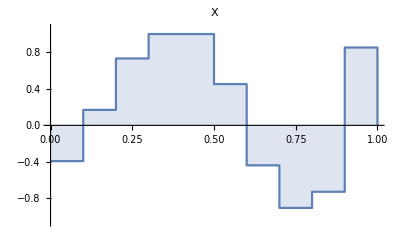
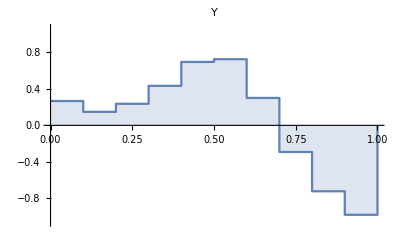

```mathematica
PulsePlot[pulse,PlotLabel->DistributeOption["X","Y"]]
```

Simulate the trajectory of some initial state:

```mathematica
BlochPlot[States@PulseSim[Hinternal,SimForm[pulse],InitialState->TP[U],PollingInterval->0.01],BlochPlotJoined->True]
```

-Graphics3D-

### Distortion Example

We use an exponential ringdown distortion. There are 5 output time steps per input time step. We use 70 output time steps instead of 10*5=50 because this way the tail of the pulse is actually used in the unitary propagator calculation.

```mathematica
distortion=LiftDistortionRank@ExponentialDistortion[0.1,10,70,0.1,0.02];
initialGuess:=RandomSmoothPulse[0.1,10,controlRange];
```

```mathematica
controlRange={{-1,1},{-1,1}};
target=MatrixExp[-I π Spin[X][1/2]/2];
Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
Hinternal=0Spin[Z][1/2];
pulse=FindPulse[initialGuess,target,0.9999,controlRange,Hcontrol,Hinternal,DistortionOperator->distortion,Repetitions->50];
```

Plot the resulting predistorted and post-distorted pulse.

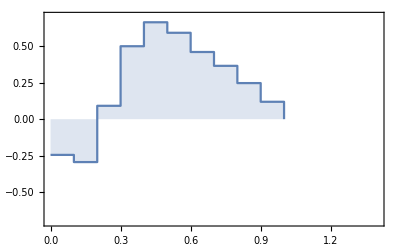
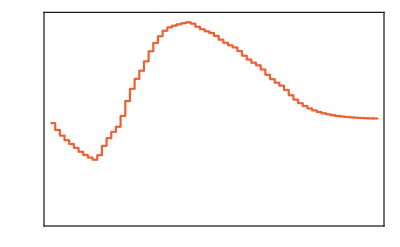
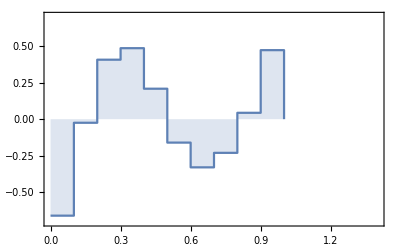
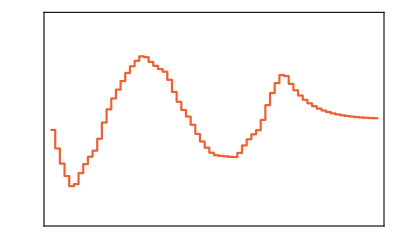

```mathematica
PulsePlot[pulse,ShowDistortedPulse->True]
```

Show the trajectory of the +Z state as it evolves under the pulse sequence. We plot both the final pulse with the distortion operator and without the distortion operator to show that not including the distortion operator, in this case, would result in much worse gate performance.

```mathematica
BlochPlot[{
States@PulseSim[Hinternal,SimForm[pulse,False],InitialState->TP[U],PollingInterval->0.01],
States@PulseSim[Hinternal,SimForm[pulse,True],InitialState->TP[U],PollingInterval->0.01]
},BlochPlotJoined->True,BlochPlotLabels->{"Without Distortion","With Distortion"}]
```

-Graphics3D-

### Distribution Example

In this example, we find a pulse with 0.99 fidelity at two offset frequencies of the internal Hamiltonian.

```mathematica
Hinternal=2π δω Spin[Z][1/2];
dist={{1/2,1/2},{{δω->-1},{δω->1}}};
```

```mathematica
controlRange={{-1,1},{-1,1}};
initialGuess:=RandomSmoothPulse[0.1,10,controlRange];
target=MatrixExp[-I π Spin[X][1/2]/2];
Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
pulse=FindPulse[initialGuess,target,0.99,controlRange,Hcontrol,Hinternal,ParameterDistribution->dist];
```

Plot the robustness vs our parameter of interest δω.

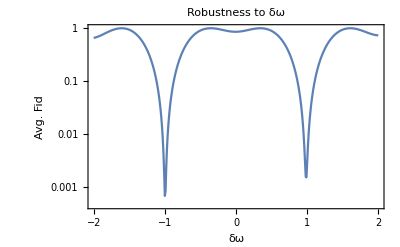

```mathematica
RobustnessPlot[pulse,δω->{-2,2,0.01},{},Joined->True,PlotLabel->"Robustness to δω",AxesLabel->{"δω","Avg. Fid"},PlotTheme->"Detailed",PlotRange->All]
```

### Monitor Example

Make sure the Preamble section has been run and evaluate the following cells to see different MonitorFunctions. It is also not too hard to write your own MonitorFunction.
We use a “pausing distortion” to slow down the iterations to make the Monitor functions actually visible.

```mathematica
controlRange={{-1,1},{-1,1}};
target:=MatrixExp[-I π Spin[X][1/2]/2];
Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
Hinternal=0Spin[Z][1/2];
pausingDistortion[t_]:=DistortionOperator[Function[{pulse,computeJac},Pause[t];IdentityDistortion[][pulse,computeJac]]];
```

#### FidelityMonitor

```mathematica
initialGuess:=RandomSmoothPulse[0.1,10,controlRange];
FindPulse[initialGuess,target,0.99,controlRange,Hcontrol,Hinternal,MonitorFunction->FidelityMonitor,DistortionOperator->pausingDistortion[.1]];
```

#### HistogramMonitor

HistogramPulsePlot shows utility values at all failed attempts trying to get to target utility.

```mathematica
initialGuess:=RandomSmoothPulse[RandomReal[{0.001,0.0021}],10,controlRange];
FindPulse[initialGuess,target,.99,controlRange,Hcontrol,Hinternal,MonitorFunction->HistogramMonitor,DistortionOperator->pausingDistortion[.01],Repetitions->15,MinimumImprovement->10^-3];
```

#### PulsePlotMonitor

A bit expensive, but nice, PulsePlotMonitor shows the current pulse as it evolves.

```mathematica
initialGuess:=RandomSmoothPulse[0.1,10,controlRange];
pulse=FindPulse[initialGuess,target,0.999,controlRange,Hcontrol,Hinternal,MonitorFunction->PulsePlotMonitor[],DistortionOperator->pausingDistortion[.3]];
```

### Penalty Example

In this example we use a penalty to suppress ringdown.

```mathematica
controlRange={{-1,1},{-1,1}};
distortion=LiftDistortionRank@ExponentialDistortion[0.1,10,70,0.1,0.02];
initialGuess:=RandomSmoothPulse[0.1,10,controlRange];
penalty=DemandValuePenalty[1,Array[{1,1}If[#>=50,1,0]&,70],0,3];
```

```mathematica
target=MatrixExp[-I π Spin[X][1/2]/2];
Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
Hinternal=0Spin[Z][1/2];
pulse=FindPulse[initialGuess,target,0.999,controlRange,Hcontrol,Hinternal,DistortionOperator->distortion,Repetitions->50,PulsePenalty->penalty,MonitorFunction->PulsePlotMonitor[ShowDistortedPulse->True]];
```

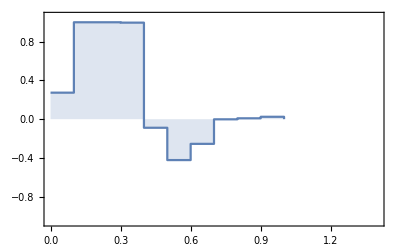
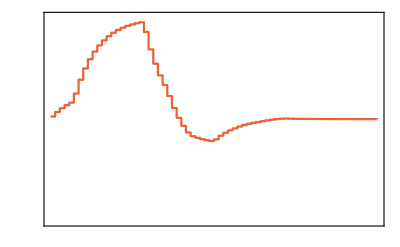
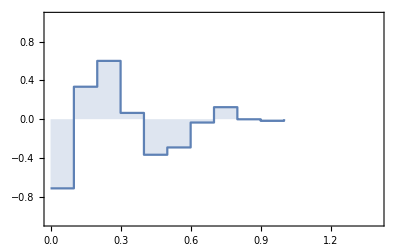
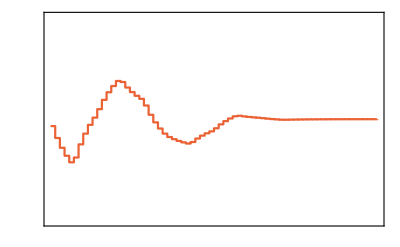

```mathematica
PulsePlot[pulse,ShowDistortedPulse->True]
```

```mathematica
pulse
```

Head | Value
UtilityValue | 0.999657
PenaltyValue | 0.000534425
ExitMessage | Pulse of desired fidelity was found!
Target | (1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))
InternalHamiltonian | (0 | 0
0 | 0)
ControlHamiltonians | (0 | π
π | 0),(0 | -ⅈ π
ⅈ π | 0)
AmplitudeRange | {{-1,1},{-1,1}}
TimeSteps | {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}
Pulse | (0.273517 | 1 | 1 | 0.9961 | -0.0885917 | -0.422105 | -0.254725 | -0.00145902 | 0.00899176 | 0.0247281
-0.713967 | 0.334857 | 0.60151 | 0.0647096 | -0.367192 | -0.291698 | -0.0346556 | 0.123771 | -0.00112956 | -0.017265)
ParameterDistribution | {{1},{{}}}
DistortionOperator | ExponentialDistortion[0.1]^(⊗numInputChannels)
PulsePenalty | DemandValuePenalty[0]

## Pulses

Pulses are generally stored in one of two formats. First, and more basic, is as a matrix of time step lengths and amplitudes of the form {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32,...},...} as used, for example, in the initialGuess argument to FindPulse. 
The second format, Pulse objects, are explained below and contain metadata such as Hamiltonians and distortion operators. This is the format output by FindPulse.

Pulse is a Head to store the output of FindPulse containing a list of rules from keys to values. For example, the output of FindPulse might be 
p=Pulse[TimeSteps->{0.1,0.1,0.1},Pulse->{{1,2},{2,0},{3,1}},UtilityValue->0.9994,...].

Retreiving Values
Like an Association, values of keys can be retreived by calling the key: p[TimeSteps]

Notes
• Pulse objects can be visualized using PulsePlot.
• Pulse serves an alternate role as a key to the pulse amplitudes of the solution found by FindPulse.

Possible Keys
UtilityValue
PenaltyValue
TimeSteps
Pulse
Target
ControlHamiltonians
InternalHamiltonian
DistortionOperator
PulsePenalty
ParameterDistribution
AmplitudeRange
ExitMessage

### Pulse Object Keys

UtilityValue is a key for Pulse whose value is the utility function value of the solution found by FindPulse.

PenaltyValue is a key for Pulse whose value is the PenaltyFunction value of the solution found by FindPulse.

TimeSteps is a key for Pulse whose value is a list of time step lengths for the solution found by FindPulse.

Pulse is a valid key for Pulse  which stores the amplitudes of the pulse.

Target is a key for Pulse whose value is the target entered as an argument to FindPulse.

ControlHamiltonians is a key for Pulse whose value is the list Hcontrol entered as an argument to FindPulse.

InternalHamiltonian is a key for Pulse whose value is the Hamiltonian Hint entered as an argument to FindPulse.

DistortionOperator is a valid key for Pulse which stores the distortion operator that acts on the input pulse.

PulsePenalty is a valid key for Pulse which stores the penalty function.

ParameterDistribution is a valid key for Pulse  which stores the distribution of parameters.

AmplitudeRange is a key for Pulse whose value is the amplitudeRange entered as an argument to FindPulse.

ExitMessage is a key for Pulse whose value is the exit message of FindPulse.

### Pulse Key Modification

PulseRemoveKeys[pulse,key1,key2,...] returns a new Pulse object with the given keys and their values removed from the Pulse object pulse.

PulseReplaceKey[pulse,key,newval] returns a new Pulse object with the value of the given key replaced with newval in the Pulse object pulse.

PulseHasKey[pulse,key] returns True iff key is one of the keys of pulse.

### Pulse Conversion and Transformation

SimForm[pulse,distort] converts a Pulse object pulse into the ShapedPulseQ format accepted by QSim`s PulseSim. If the optional argument distort is True (default value),  the DistortionOperator is called on the pulse.

ToPulse[pulsemat] turns the matrix pulsemat of the form {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32},...} into a Pulse object where all keys besides Pulse and TimeSteps are set to nominal qubit values.

Options
ToPulse accepts any of the following options whose values will override the default nominal values, for example, ToPulse[...,InternalHamiltonian->TP[X],...]
UtilityValue, PenaltyValue, Target, ControlHamiltonians, InternalHamiltonian, DistortionOperator, PulsePenalty, ParameterDistribution, AmplitudeRange, ExitMessage

FromPulse[pulse] turns the Pulse object pulse into a pulse matrix with format {{dt1,a11,a12,...},{dt2,a21,a22,...},{dt3,a31,a32},...}.

AddTimeSteps[dts,amplitudes] returns a pulse matrix with given time steps and amplitudes.

SplitPulse[pulseMat] returns {pulseMat⟦All,1⟧,pulseMat⟦All,2;;-1⟧}.

#### Example

```mathematica
pulsemat={{1,1,1},{2,3,4},{5,6,7}};
```

```mathematica
ToPulse[pulsemat]
```

Head | Value
UtilityValue | None
PenaltyValue | 0
ExitMessage | Generated by ToPulse.
Target | (1 | 0
0 | 1)
InternalHamiltonian | (0 | 0
0 | 0)
ControlHamiltonians | (0 | π
π | 0),(0 | -ⅈ π
ⅈ π | 0)
AmplitudeRange | {{-1,1},{-1,1}}
TimeSteps | {1,2,5}
Pulse | (1 | 3 | 6
1 | 4 | 7)
ParameterDistribution | None
DistortionOperator | IdentityDistortion[]
PulsePenalty | ZeroPenalty[]

```mathematica
FromPulse[ToPulse[pulsemat]]
```

{{1,1,1},{2,3,4},{5,6,7}}

```mathematica
SimForm[ToPulse[pulsemat]]
```

{{{1,1,1},{2,3,4},{5,6,7}},{{{0,2 π},{2 π,0}},{{0,-2 ⅈ π},{2 ⅈ π,0}}}}

### Pulse Manipulation

PulsePhaseRotate[pulse,ϕ] returns a new Pulse object where the phase between the amplitudes of the Pulse object pulse are rotated by a constant angle ϕ (radians). It is assumed that there are two amplitude values per time step.

PulsePhaseRamp[pulse,f] returns a new Pulse object where the pulse has been phase ramped with a slope 2π*f. The pulse is assumed to have two amplitudes per step, and is in x-y coordinates.

PulseModulate[pulse,f] returns a new Pulse object where the pulse has been cosine modulated at an angular frequency 2π*f. The pulse is assumed to have two amplitudes per step, and is in x-y coordinates.
PulseModulate[pulse,f,ϕ] returns a new Pulse object where the pulse has been modulated at an angular frequency 2π*f and a modulation phase ϕ. Here, ϕ=0 is equivalent to cosine modulation, and ϕ=π/2 is equivalent to sine modulation.

PulseDivide[pulse,n] returns a new Pulse object where each time step has been evenly divided into n steps.

#### Example 1

Rotate a pulse with Gaussian tails by angle π/4.

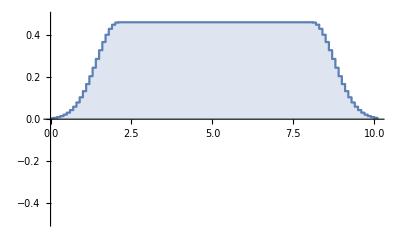
-Graphics--Graphics-

```mathematica
PulsePhaseRotate[GaussianTailsPulse[0.1,10,2,Area->5]//ToPulse,π/4]//PulsePlot
```

#### Example 2

Phase ramp a pulse with Gaussian tails by a frequency of 0.5.

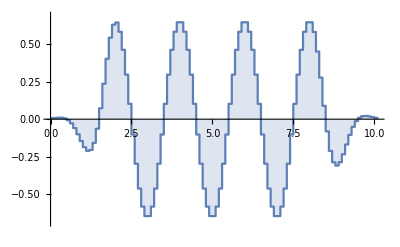
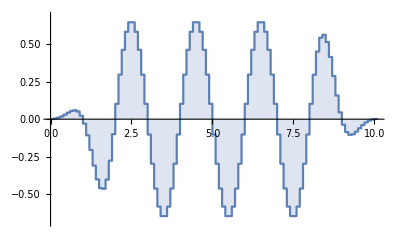

```mathematica
PulsePhaseRamp[GaussianTailsPulse[0.1,10,2,Area->5]//ToPulse,.5]//PulsePlot
```

#### Example 3

Define a square pulse with a parameter specifying offset frequency in the internal hamiltonian, and a target which wants to invert the populations of the |0⟩ and |1⟩ states.

```mathematica
pulseFn[amp_]:=PulseDivide[ToPulse[
{{.5,amp,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
Target->CoherentSubspaces[{({{1}, {0}}),({{0}, {1}})},{({{0}, {1}}),({{1}, {0}})}]
],100];
```

Plot the ability to invert population as a function of offset frequency. We see that:
• Square pulse does best at 0 offset, as expected.
• Phase ramping moves the peak to the right by 5 units.
• Modulating by 3 moves the peak to positive and negative 3. Note that we need to double the power.

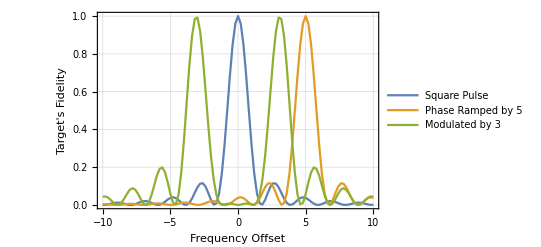

```mathematica
RobustnessPlot[{pulseFn[1],PulsePhaseRamp[pulseFn[1],5],PulseModulate[pulseFn[2],3]},δω->{-10,10,.2},{},
Joined->True,PlotRange->{0,1},LogPlot->False,PlotLegends->{"Square Pulse","Phase Ramped by 5","Modulated by 3"},FrameLabel->{"Frequency Offset","Target's Fidelity"},PlotTheme->"Detailed"
]
```

#### Example 4

Make a pulse with two time steps.

```mathematica
pulse=ToPulse[{{1,2,3},{4,5,6}}];
```

Divide each time step into ten pieces.

```mathematica
pulse[TimeSteps]
PulseDivide[pulse,10][TimeSteps]
```

{1,4}

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5,2/5}

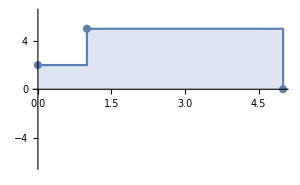
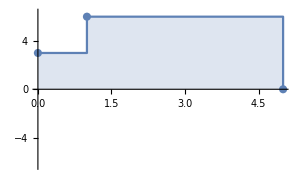

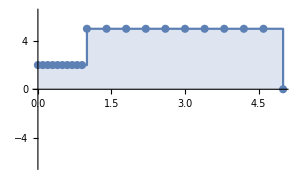
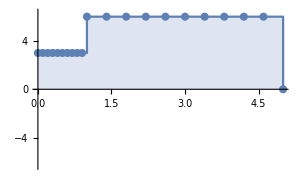

```mathematica
PulsePlot[pulse,ImageSize->300,Mesh->Full]
PulsePlot[PulseDivide[pulse,10],ImageSize->300,Mesh->Full]
```

### Pulse Matrix Generation

RandomPulse[dts,controlRange] returns a pulse matrix with given time steps dts and amplitudes chosen uniformly at random from the given controlRange.
RandomPulse[dt,n,controlRange] returns a pulse matrix with n time steps of length dt and amplitudes chosen uniformly at random from the given controlRange.

RandomSmoothPulse[dts,controlRange] returns a pulse matrix with given time steps dts and amplitudes with a smooth profile with limits set by controlRange.
RandomSmoothPulse[dt,n,controlRange] returns a pulse matrix with n time steps of length dt and amplitudes with a smooth profile with limits set by controlRange.

Options
InterpolationPoints, by default 10, specifies the interval at which random amplitudes are chosen. The intermediate amplitudes are interpolated with a spline.

GenerateAnnealedPulse[originalPulse,controlRange] returns a pulse that perturbs originalPulse by a new random pulse with limits set by controlRange.

Options
AnnealingGenerator specifies the function to use that generates random pulses. The default is RandomPulse.

GaussianTailsPulse[dt,T,riseTime,Area→A] returns a pulse matrix with a flat top and Gaussian tails. This pulse has two control channels and stepsize dt, total time T (rounded to the nearest dt), total area A, and tails each with length riseTime.
GaussianTailsPulse[dt,T,riseTime,Max→max] returns a pulse matrix with a flat top and Gaussian tails. This pulse has two control channels and stepsize dt, total time T (rounded to the nearest dt), maximum value max, and tails each with length riseTime.

#### Options

AnnealingGenerator is an option for GenerateAnnealPulse which specifies the function to use that generates random pulses.

#### Example 1

Generate a few random pulses.

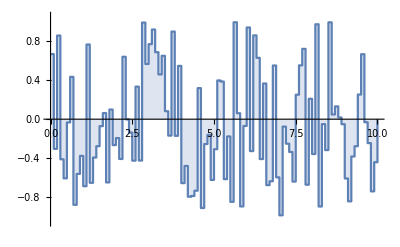
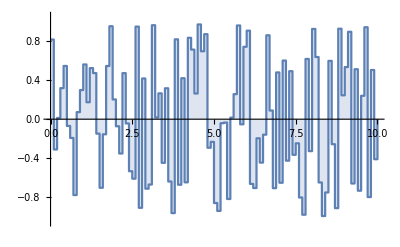

```mathematica
RandomPulse[.1,100,{{-1,1},{-1,1}}]//ToPulse//PulsePlot
```

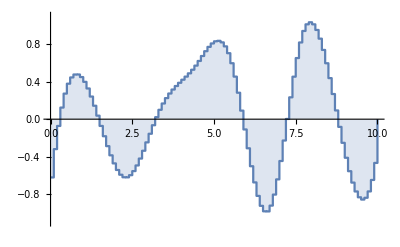
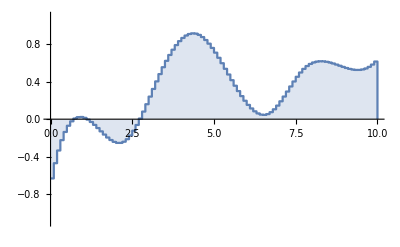

```mathematica
RandomSmoothPulse[.1,100,{{-1,1},{-1,1}}]//ToPulse//PulsePlot
```

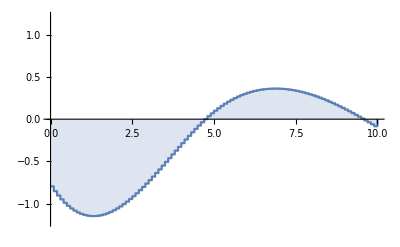
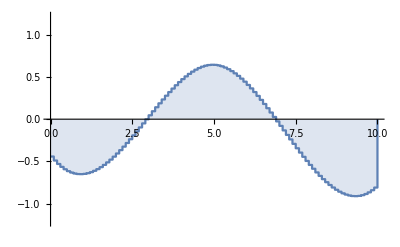

```mathematica
RandomSmoothPulse[.1,100,{{-1,1},{-1,1}},InterpolationPoints->50]//ToPulse//PulsePlot
```

#### Example 2

Anneal a pulse with 10% random fluctuations.

```mathematica
origPulse=RandomSmoothPulse[0.1,100,{{-1,1},{-1,1}}];
newPulse=GenerateAnnealedPulse[origPulse,0.1*{{-1,1},{-1,1}}];
```

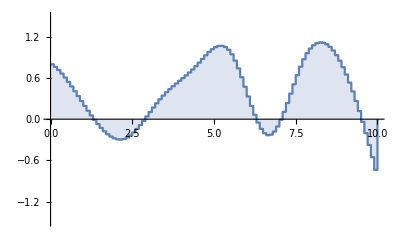
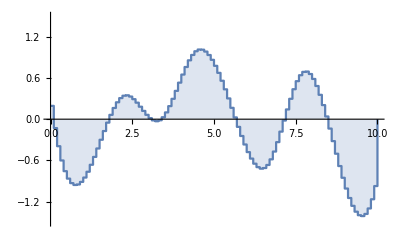

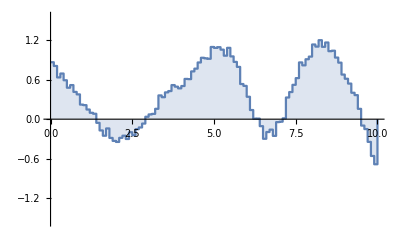
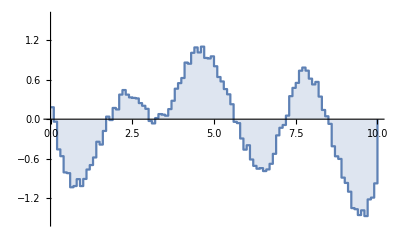

```mathematica
origPulse//ToPulse//PulsePlot
newPulse//ToPulse//PulsePlot
```

#### Example 3

Gaussian tails with total area of 5.

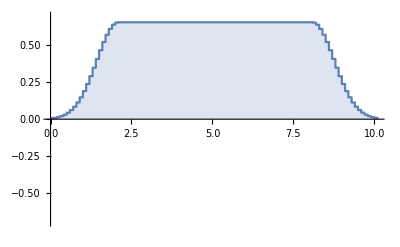
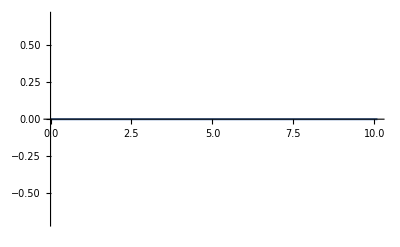

```mathematica
GaussianTailsPulse[0.1,10,2,Area->5]//ToPulse//PulsePlot
```

Gaussian tails with maximum amplitude of 5.

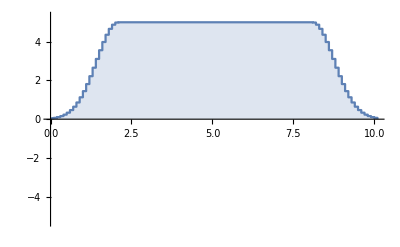
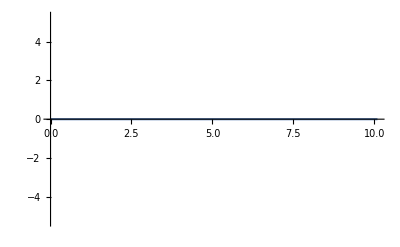

```mathematica
GaussianTailsPulse[0.1,10,2,Max->5]//ToPulse//PulsePlot
```

### Legalization and Normalization

LegalizePulse[pulseMat,controlRange] returns a new pulse matrix where the pulse amplitudes in the pulse matrix pulseMat have been clipped to the limits given in controlRange.
LegalizePulse[profile][pulseMat,controlRange] returns a new pulse matrix where the pulse amplitudes in the pulse matrix pulseMat have been clipped to the limits given in controlRange, multiplied by the value of the profile value at the given time step. The profile argument should be a list with the same length as pulseMat. Note that the profile can be a 1D array, in which case each control channel will see the same profile, or an array whose second dimension equals the number of control channels, in which cas each control channel may see a different profile.

NormalizePulse[pulse,controlRange] scales and translates the pulse amplitues in the pulse matrix pulseMat to the interval [0,1] using controlRange as a reference.

#### Example 1

Clip the first channel at amplitude 1, and the second channel at amplitude 1.5.

```mathematica
illegalPulse=RandomSmoothPulse[.1,100,{{-3,3},{-3,3}}];
legalPulse=LegalizePulse[illegalPulse,{{-1,1},{-1.5,1.5}}];
```

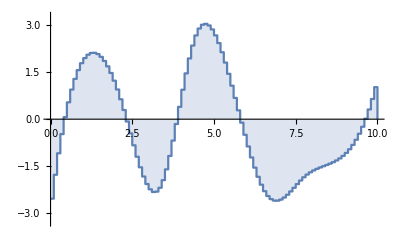
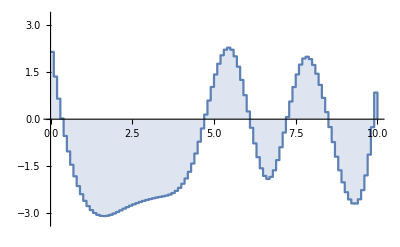

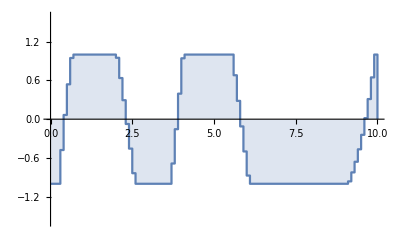
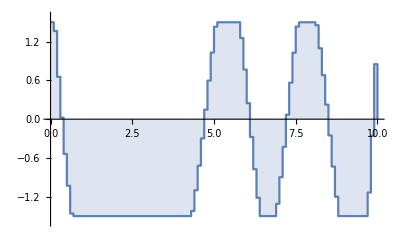

```mathematica
illegalPulse//ToPulse//PulsePlot
legalPulse//ToPulse//PulsePlot
```

#### Example 2

Use the GaussianTailsPulse function as a convenience function to create a 1D profile list.

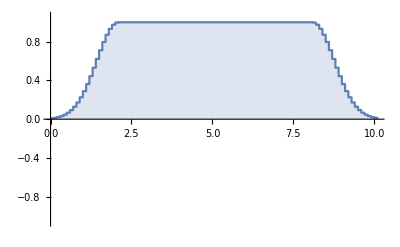
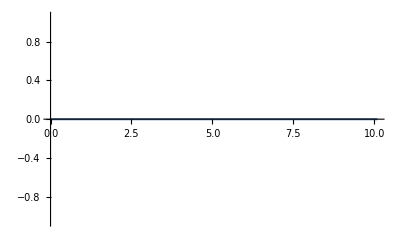

```mathematica
profile=GaussianTailsPulse[.1,.1*100,2,Max->1];
PulsePlot[ToPulse@profile]
profile=profile[[All,2]];
```

The pulse is now clipped to the shown profile

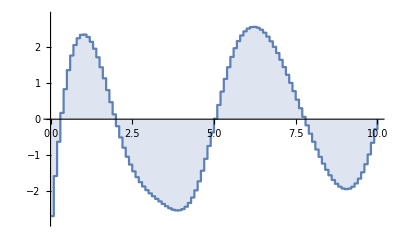
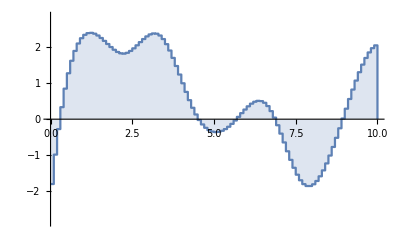

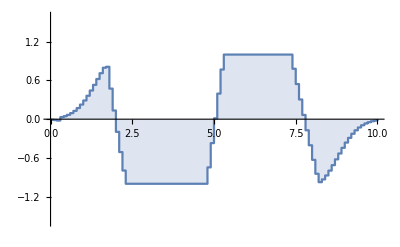
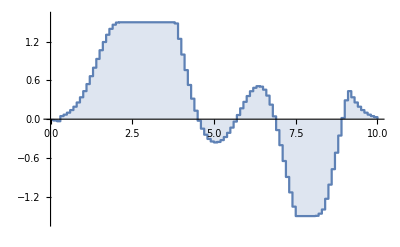

```mathematica
illegalPulse=RandomSmoothPulse[.1,100,{{-3,3},{-3,3}}];
legalPulse=LegalizePulse[profile][illegalPulse,{{-1,1},{-1.5,1.5}}];
illegalPulse//ToPulse//PulsePlot
legalPulse//ToPulse//PulsePlot
```

Note that if the profile can specify a different profile for each control channel.

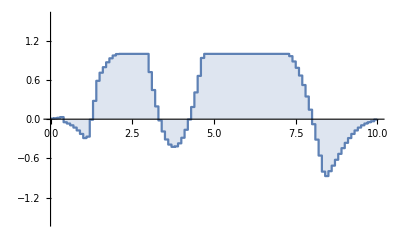
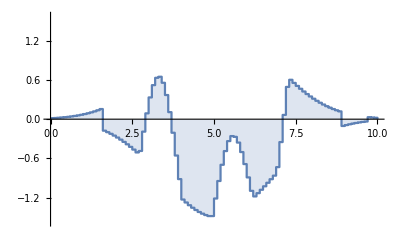

```mathematica
profile1=GaussianTailsPulse[.1,.1*100,2,Max->1];
profile2=GaussianTailsPulse[.1,.1*100,5,Max->1];
profile={profile1[[All,2]],profile2[[All,2]]}ᵀ;
legalPulse=LegalizePulse[profile][illegalPulse,{{-1,1},{-1.5,1.5}}];
legalPulse//ToPulse//PulsePlot
```

#### Example 3

Clip the first channel at amplitude 1, and the second channel at amplitude 1.5.

```mathematica
abnormalPulse=RandomSmoothPulse[.1,100,{{-12,-10},{-4,5}}];
normalPulse=NormalizePulse[abnormalPulse,{{-12,-10},{-4,5}}];
```

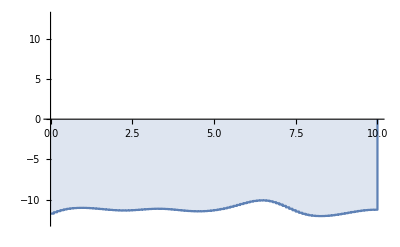
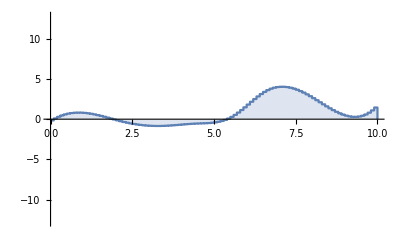

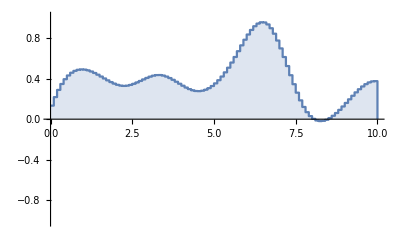
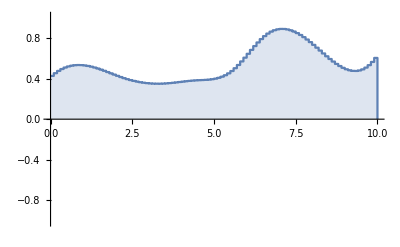

```mathematica
abnormalPulse//ToPulse//PulsePlot
normalPulse//ToPulse//PulsePlot
```

## Utility Function and Targets

Utility[S,target] returns the utility function value of the propagator S with respect to the target. In a closed system, S will be a unitary matrix corresponding to the time evolution of a given pulse. The particular utility function invoked will depend on the target. If target is a matrix, the average fidelity (|Tr(target†.S)/d|)^2 will be used. Other possible forms of target are CoherentSubspaces and StateToState.

Note	
In the presence of a ParameterDistribution, S will correspond to a single point from the distribution and hence will still be unitary in the case where the system is closed, even though the effective map weighted over all elements of the ParameterDistribution will be in general be non-unitary.

UtilityGradient[pulse,Hint,Hcontrol,target] returns a tuple {utilityValue,gradient} where utilityValue is the value of Utility with the given pulse and Hamiltonians and gradient is the gradient of the utility function at the same point. The gradient will be an array of dimensions equal to that of pulse, where pulse is in the format of initialGuess from FindPulse. See Utility for a description of target.

PropagatorFromPulse[pulse,Hint,Hcontrol] returns the total evolution propagator S (as seen by Utility) due to the given pulse and Hamiltonians. In the case of a closed system, S will be a unitary matrix.

Note
This function is used by UtilityGradient when evaluating utilityValue.

PropagatorListFromPulse[pulse,Hint,Hcontrol] returns a list of propagators due to each step in the given pulse evolving under the given Hamiltonians. In the case of a closed system, this will be a list of unitary matrices.

Note
This function is used by UtilityGradient when evaluating the gradient.

### Coherent Subspaces

CoherentSubspaces is a type of target for FindPulse. CoherenteSubspaces[{X1,...,Xn},{Y1,...,Yn}] tries to find a pulse which produces a unitary U such that U.X_k=ⅇ^(i ϕ_k)Y_k for all 1≤k≤n where ϕ_k is an arbitrary phase. If each index k is represents a different orthogonal subspace of the Hilbert space, then this utility function essentially asks for a unitary that preserves relative phases within each subspace, but does not care what the phase is between subspaces. This is implemented as

	∑_(k=1)^n |Tr[(U.X_k)†.Y_k]/n_k|^2/n

where n_k is equal to Length[Xk]. It is straightforward to prove that this quantity lies between 0 and 1, and that it is equal to 1 if and only if the relationship described above is true.

Note
For this to be well defined, X_k must have the same dimensions as Y_k for each k.
This will not always be possible. For example, if the X_k’s are pairwise orthogonal, but the Y_k’s are not, no unitary will be able to acheive the maximum utility value.

### StateToState

## Distortion Operators

DistortionOperator is an option to FindPulse which specifies an operator which distorts the input pulse.

DistortionOperator[distortion] is a Head storing the function distortion which evaluates with the arguments distortion[inputPulse,computeJacobian]. It holds that DistortionOperator[distortion][arguments]=distortion[arguments]; that is, DistortionOperator[distortion] is effectively callable with function values computed by distortion.

DistortionOperator[distortion,format] is equivalent to DistortionOperator[distortion], except that, additionally, a human readable format expression is included. Whenever Format[DistortionOperator[distortion,format]] is invoked, format is returned.

Function Arguments
•  The input pulse is expected in the same format as FindPulse’s argument initialGuess; {{dt1,a11,...,a1K},{dt2,a21,...,a2K},...,{dtN,aN1,...,aNK}} where the dt’s are pulse lengths and the a’s are input pulse amplitudes, and there are K input control channels and N input control time steps.
• If computeJacobian is False, no Jacobian tensor is returned, and the output is in the form {{dt1,a11,...,a1L},{dt2,a21,...,a2L},...,{dtM,aM1,...,aML}}, such that there are L output control channels and M output control time steps.
• If computeJacobian is True, the output is of the form {outputPulse,jacobian}, where outputPulse=distortion[pulse,False], and jacobian is the rank four Jacobian tensor of distortion at pulse with Dimensions equal to {M,L,N,K}.
• If computeJacobian is All, the output is of the form {inputPulse,modifiedInputPulse,outputPulse} where inputPulse is equal to the pulse input into the distortion operator, outputPulse is the final distorted pulse, and modifiedInputPulse is an intermediate pulse (which will usually be equal to inputPulse). 
 
Notes
• The function FindPulse accepts the argument DistortionOperator, which should have a Head equal to DistortionOperator and act as described above.
• The modifiedInputPulse mentioned above is useful in some situations where the notion of what an input pulse should be is different in the context of GRAPE compared to the context one’s actual control hardware. For example, with ringdown suppression, additional pulse steps will be appended to an input pulse given to GRAPE in order to cancel ringdown, whereas the control hardware will presumably need to have these additional steps in advance, and so should be a part of the controller’s input pulse. The modifiedInputPulse will therefore contain these extra “input” time steps, but the inputPulse will not.

### Distortion Operator Tools

LiftDistortionRank[distortion], when provided with a DistortionOperator distortion with a single input and output channel, returns a new distortion that acts this distortion on each channel of a given input pulse. This function is useful if all input channels feel the same distortion.

JoinDistortions[distortion1,distortion2,...] joins K single-channel DistortionOperators into a single new DistortionOperator with K channels.

ComposeDistortions[distortion1,distortion2,...] returns a new DistortionOperator which is the composition of the input DistortionOperators. distortion1 is applied first, distortion2 second, and so on.

Notes
• The new DistortionOperator, when called with computeJac set to All, will give an output equal to the last distortion called with All whose inputPulse is equal to the composition of all prior distortions.

PerturbateDistortion[distortion] adds the definition distortion[pulse,True] to the given DistortionOperator distortion, where distortion[pulse,False] is assumed to be already already defined. This is done by taking a finite difference at each input pulse time step and channel.

#### Example 1

Define two DistortionOperators, the second is lifted from the first.

```mathematica
d1=ExponentialDistortion[0.5,5,10,1,0.5]
d2=LiftDistortionRank[d1]
```

ExponentialDistortion[0.5]

ExponentialDistortion[0.5]^(⊗numInputChannels)

d1 works on a single channel pulse, but would fail on a 2-channel pulse.

```mathematica
d1[{{1,1},{1,2},{1,3},{1,4},{1,5}},False]
```

{{0.5,0.393469},{0.5,0.77687},{0.5,1.31138},{0.5,1.74667},{0.5,2.30028},{0.5,2.74259},{0.5,3.29877},{0.5,3.74203},{0.5,4.29857},{0.5,4.74196}}

However, with LiftDistortionRank, it will apply d1 to any number of input channels:

```mathematica
d2[{{1,1,1},{1,2,2},{1,3,3},{1,4,4},{1,5,5}},False]
```

{{0.5,0.393469,0.393469},{0.5,0.77687,0.77687},{0.5,1.31138,1.31138},{0.5,1.74667,1.74667},{0.5,2.30028,2.30028},{0.5,2.74259,2.74259},{0.5,3.29877,3.29877},{0.5,3.74203,3.74203},{0.5,4.29857,4.29857},{0.5,4.74196,4.74196}}

#### Example 2

Define a distortion that has a 0.5 length risetime on channel 1, and  a 0.2 length risetime on channel 2.

```mathematica
d=JoinDistortions[ExponentialDistortion[0.5,5,10,1,0.5],ExponentialDistortion[0.2,5,10,1,0.5]]
```

(ExponentialDistortion[0.5]
ExponentialDistortion[0.2])

```mathematica
d[{{1,1,1},{1,2,2},{1,3,3},{1,4,4},{1,5,5}},False]
```

{{0.5,0.393469,0.713495},{0.5,0.77687,0.976482},{0.5,1.31138,1.71156},{0.5,1.74667,1.97632},{0.5,2.30028,2.71155},{0.5,2.74259,2.97632},{0.5,3.29877,3.71155},{0.5,3.74203,3.97632},{0.5,4.29857,4.71155},{0.5,4.74196,4.97632}}

#### Example 3

Two exponential distortions in a row.

```mathematica
d=ComposeDistortions[ExponentialDistortion[0.5,5,10,1,0.5],ExponentialDistortion[0.5,10,20,0.5,0.25]]
```

ExponentialDistortion[0.5]○ExponentialDistortion[0.5]

```mathematica
d[{{1,1},{1,2},{1,3},{1,4},{1,5}},False]
```

{{0.25,0.0870351},{0.25,0.207608},{0.25,0.365546},{0.25,0.52739},{0.25,0.743787},{0.25,0.967119},{0.25,1.19886},{0.25,1.41441},{0.25,1.6676},{0.25,1.91654},{0.25,2.16537},{0.25,2.39248},{0.25,2.65327},{0.25,2.90725},{0.25,3.15935},{0.25,3.38862},{0.25,3.65078},{0.25,3.90567},{0.25,4.15834},{0.25,4.38797}}

#### Example 4

Define a distortion that doubles pulse amplitudes, but doesn’t compute the Jacobian tensor. Call PerturbateDistortion on this.

```mathematica
d=DistortionOperator[Function[{pulse,computeJac},AddTimeSteps[pulse⟦All,1⟧,2pulse⟦All,2;;-1⟧]],"myDistortion"]
pd=PerturbateDistortion[d]
```

myDistortion

PerturbateDistortion[myDistortion]

The distortion operator d will not give us a Jacobian tensor (this would cause errors if we were to use it in GRAPE):

```mathematica
d[{{1,2},{1,3}},True]
```

{{1,4},{1,6}}

But pd will:

```mathematica
pd[{{1,2},{1,3}},True]
```

{{{1,4},{1,6}},{{{{2},{0}}},{{{0},{2}}}}}

### IdentityDistortion

IdentityDistortion[] returns a DistortionOperator whose output pulse is equal to its input pulse. This is the default value of DistortionOperator in FindPulse.

#### Example

```mathematica
id=IdentityDistortion[]
id[{{1,1},{1,2},{1,3}},True]
```

IdentityDistortion[]

{{{1,1},{1,2},{1,3}},{{{{1},{0},{0}}},{{{0},{1},{0}}},{{{0},{0},{1}}}}}

### Variable Change Distortions

TimeScaleDistortion[multiplier] returns a DistortionOperator that multiplies the input time step values by multiplier.

VariableChangeDistortion[changeFn,variableSymbol] returns a DistortionOperator that performs a per-time-step change of variable on the single-channel input pulse. This is the most general type of distortion function where different time steps don’t affect each other. To compute the Jacobian tensor, it is assumed that the functions are analytically differentiable
VariableChangeDistortion[{changeFn1,changeFn2,...}, {variableSymbol1,variableSymbol2,...}] is the multiple channel version of the above, where each channel gets its own function.

Options
Simplify->True specifies that Simplify should be called on the per-step Jacobian as the distortion operator is initialized.

Example
VariableChangeDistortion[{a*Cos[ϕ],a*Sin[ϕ]},{a,ϕ}] changes from polar coordinates to cartesian coordinates in a two channel system.

#### Example 1

Multiply all of the time steps by 2.

```mathematica
d=TimeScaleDistortion[2]
d[{{1,1},{1,2},{1,3}},False]
```

TimeScaleDistortion[2]

{{2,1},{2,2},{2,3}}

#### Example 2

The Jacobian is automatically symbolically calculated in this change of coordinates distortion from polar to cartesian.

```mathematica
d=VariableChangeDistortion[{a*Cos[ϕ],a*Sin[ϕ]},{a,ϕ}]
d[{{dt,a1,b1},{dt,a2,b2}},True]//Column
```

VariableChangeDistortion[{a,ϕ}→{a Cos[ϕ],a Sin[ϕ]}]

{{dt,a1 Cos[b1],a1 Sin[b1]},{dt,a2 Cos[b2],a2 Sin[b2]}}
{{{{Cos[b1],-a1 Sin[b1]},{0,0}},{{Sin[b1],a1 Cos[b1]},{0,0}}},{{{0,0},{Cos[b2],-a2 Sin[b2]}},{{0,0},{Sin[b2],a2 Cos[b2]}}}}

### Linear Distortions

ConvolutionDistortion[kernel,numInput,numOutput,dtInput,dtOutput] returns a distortion function which convolves the input pulse with the given kernel in the time domain to get the output pulse. The kernel should be a single valued function that outputs a number, in the case of one input and one output channel, or a matrix of dimensions {L,K}, in the case of K input channels and L output channels. numInput and numOutput are respectively the number of input and output time steps. dtInput and dtOutput are respectively the (constant sized) input and output timestep lengths.

ConvolutionDistortion[kernelIntegral,numInput,numOutput,dtOutput] provides slightly more flexibility over the previous calling syntax by accepting an integral over the kernel rather than the kernel itself, allowing a custom integrator to be used. kernelIntegral should be a two-argument function kernelIntegral[m,n] equal to ∫_((n-1)dtInput)^(n dtInput) kernel[(m-1/2)dtOutput-τ]ⅆτ where n is the input timestep index, and m is the output timestep index.

ExponentialDistortion[τc,numInput,numOutput,dtInput,dtOutput] returns a single channel distortion that causes an exponential rise and fall time of timescale τc. numInput and numOutput are respectively the number of input and output time steps. dtInput and dtOutput are respectively the (constant sized) input and output timestep lengths.

Notes
• This function is equivalent to ConvolutionDistortion[Piecewise[{{0,#<0}},Exp[-#/τc]/τc]&,numInput,numOutput,dtInput,dtOutput], but uses a precalculated integral and is therefore faster to initialize.
• Use LiftDistortionRank or JoinDistortions to turn this into a multiple channel function.

See also LinearDEDistortion.

#### Example 1

A single channel distortion. In this case, equivalent to ExponentialDistortion.

```mathematica
d=ConvolutionDistortion[Piecewise[{{0,#<0}},Exp[-#/τc]/τc]&,2,4,1,1/2]
d[{{1,1},{1,2}},False]//Simplify
```

ConvolutionDistortion[Piecewise[{{0, #1<0}, {Exp[-#1/τc]/τc, True}}]&]

{{1/2,1-ⅇ^(-1/4/τc)},{1/2,1-ⅇ^(-3/4/τc)},{1/2,2-ⅇ^(-5/4/τc)-ⅇ^(-1/4/τc)},{1/2,2-ⅇ^(-7/4/τc)-ⅇ^(-3/4/τc)}}

#### Example 2

A multi-exponential distortion with 2 input channels and 1 output channel.

```mathematica
d=ConvolutionDistortion[Table[Piecewise[{{0,#<0}},Exp[-#/τc[L,K]]/τc[L,K]],{L,1},{K,2}]&,2,4,1,1/2]
d[{{1,1,.3},{1,2,.7}},True]//Last//Dimensions
```

ConvolutionDistortion[Table[Piecewise[{{0, #1<0}, {Exp[-#1/τc[L,K]]/τc[L,K], True}}],{L,1},{K,2}]&]

{4,1,2,2}

#### Example 3

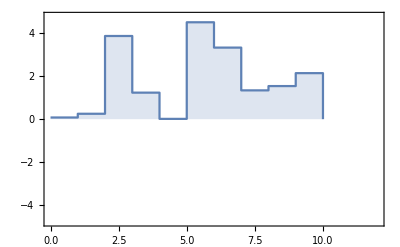
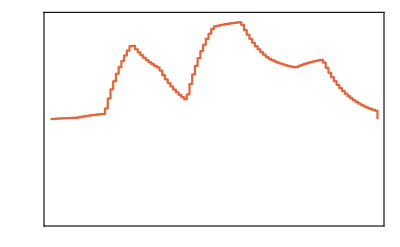

```mathematica
d=ExponentialDistortion[1,10,120,1,0.1];
inputPulse=AddTimeSteps[1,RandomReal[{0,5},{10,1}]];
PulsePlot[Pulse[TimeSteps->inputPulse⟦All,1⟧,Pulse->inputPulse⟦All,2;;⟧,DistortionOperator->d],ShowDistortedPulse->True]
```

### IQDistortion

IQDistortion[Igain,Ioffset,Qgain,Qoffset,Qθ] performs the 2-channel variable change distortion {I,Q}→{x,y} where x=(Igain*I+Ioffset)+Cos[Qθ](Qgain*Q+Qoffset), ynew=Sin[Qθ](Qgain*Q+Qoffset), and where Qθ is the angle from I to Q in an IQ mixer.

```mathematica
NDSolveValue
```

#### Example

```mathematica
IQDistortion[Igain,Ioffset,Qgain,Qoffset,Qθ]
```

VariableChangeDistortion[{Ichan$791,Qchan$791}→{Ichan$791 Igain+Ioffset+(Qchan$791 Qgain+Qoffset) Cos[Qθ],(Qchan$791 Qgain+Qoffset) Sin[Qθ]}]

### NonlinearTransferDistortion

NonlinearTransferDistortion[gainFunction] returns a DistortionOperator that performs a distortion by taking the discrete fourier transform of the pulse, multiplying every fourier component by the frequency and amplitute dependent function gainFunction[freq,amp], and then returning it to time domain. In the event that gainFunction is only a function of frequency, this will be the same as a convolution. 

Details
This function expects two input channels and output pulses have two output channels. The first input channel is interpretted as the real part of a waveform, and the second as the imaginary part; this complex waveform is discrete fourier transformed, and the elements of the resulting complex vector are fed to the amp argument of gainFunction. The freq argument of gainFunction is computed assuming uniform time spacing. The modified fourier vector is inverse transformed and returned, real and imaginary compenents being interpretted as the first and second output channels, respectively.

Notes
• It is assumed that the pulse has uniform time spacing.
• PerturbateDistortion is used to compute the Jacobian tensor.

#### Example

Define a gain function and plot it.

```mathematica
gainFcn[freq_,amp_]:=(1+0.2 Abs[amp]^2)Exp[-(Abs[freq]-5)^2/3]
Plot3D[gainFcn[freq,amp],{freq,0,10},{amp,0,5},PlotRange->All,AxesLabel->{"Freq","Amp"}]
```

-Graphics3D-

Set the input pulse to a sum of two cosines at a low frequency (1) and high frequency (5). Notice that the output pulse has the low frequency suppressed, as expected.

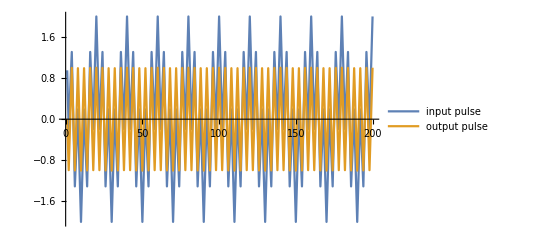

```mathematica
d=NonlinearTransferDistortion[gainFcn];
inputPulse=AddTimeSteps[0.05,Table[{Cos[2π t]+Cos[2π 5t],0},{t,0.05,10,0.05}]];
outputPulse=d[inputPulse,False];
ListPlot[{inputPulse[[All,2]],outputPulse[[All,2]]},Joined->True,PlotLegends->LineLegend[{"input pulse","output pulse"}]]
```

### DEDistortion

DEDistortion[deFn,outputForm,solnSymbol,t,min,max,δt,M] returns a DistortionOperator that distorts pulses by discretizing the solution to a set of differential equations which depend on the input pulse. 

Arguments
• deFn is a function deFn[pulse] that returns a set differential equations in a format suitable for NDSolve
•  outputForm is an expression containing symbols from solnSymbol specifying how the DE solution is related to the output pulse channels
• solnSymbol is a symbol or list of symbols representing the DE variables to solve for
• t is a symbol representing the independent DE variable
• min and max are the starting and stopping values of t to simulate for
• δt is the time interval at which to discretize the solution
• M is the number of output pulse time steps

Notes
• The output of the DE solver is an interpolating function. This function is sampled from δt to M*δt in steps of δt.
• If M*δt>max, you will receive warnings about exceeding the range of the inerpolated output of the DE solver.

Options
All options to NDSolve are valid and will be relayed to NDSolve. Additionally:
• DESolver, DESolverArgs

LinearDEDistortion[A,b,outputComponent,numInput,numOutput,dtInput,dtOutput] returns a DistortionOperator which describes the linear differential equation dx/dt=A.x(t)+f(t)b. The input pulse is assumed to have two control components which determine the real and imaginary parts of the complex forcing amplitude f(t). The output pulse is derived by taking the real and imaginary parts of the outputComponent’th element of x(t). The input and output time step numbers and durations are specified by numInput, numOutput, dtInput, and dtOutput. 

Notes
The distortion is implemented by precomputing the jacobian tensor of the discretized distortion operator. Pulses are then distorted by contracting them with this tensor; this part has exactly the same implementation as the convolution distortion. This is possible because the distortion operator is linear.

#### Options

DESolver is an option for DEDistortion that changes the solver function from NDSolve. Normally, this will be used to call ParametricNDSolve instead of the default NDSolve.

DESolverArgs is an option for DEDistortion that is a list of arguments to be given to the DESolver used by DEDistortion. This option is only necessary if the DESolver used has options other than those of NDSolve (which are accepted as normal options to DEDistortion).

#### Example 1

A simple contrived example where the initial values depend on the input pulse, which only has one time step.

```mathematica
deFn[pulse_]:={
x''[t]==-10x[t]+y[t],
y''[t]==-10y[t]-x'[t],
x[0]==pulse[[1,2]],
y[0]==pulse[[1,3]],
x'[0]==0,
y'[0]==0
};
```

We want the output to be the solution to x and the solution to y.

```mathematica
d=DEDistortion[deFn,{x[t],y[t]},{x,y},t,0,2,0.1,20]
```

DEDistortion[{x[t],y[t]}]

Example of an input pulse being distorted.

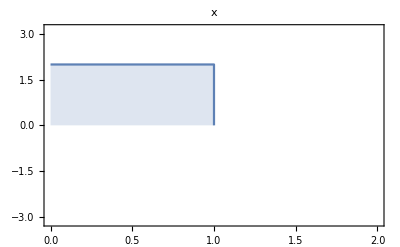
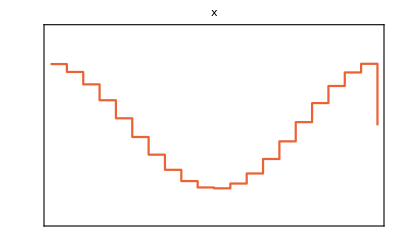
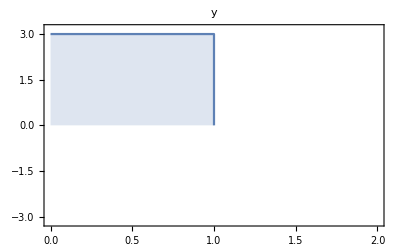
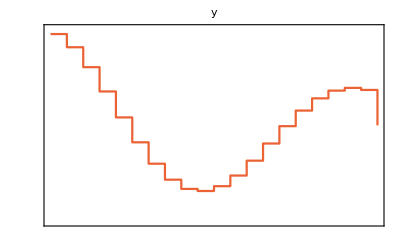

```mathematica
PulsePlot[Pulse[TimeSteps->{1},Pulse->{{2,3}},DistortionOperator->d],ShowDistortedPulse->True,PlotLabel->DistributeOption["x","y"]]
```

#### Example 2

Consider a very simple linear DE dx/dt=-5x(t)+f(t). If we force it with a piecewise constant f(t)=1 for 0<t<1 and f(t)=-5i for 1<t<2 we get the following behaviour calculated with NDSolve:

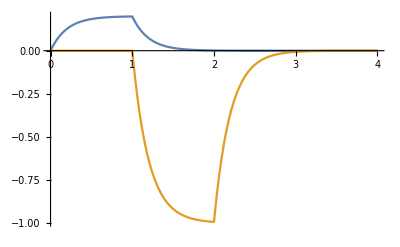

```mathematica
s=NDSolve[{x'[t]==(-5)x[t]+Piecewise[{{1,t<1},{-5I,1<t<2}},0],x[0]==0},x,{t,0,4}];
Plot[{Evaluate[Re[x[t]]/.s],Evaluate[Im[x[t]]/.s]},{t,0,4},PlotRange->All]
```

This can be replicated in a discretized fashion with LinearDEDistortion:

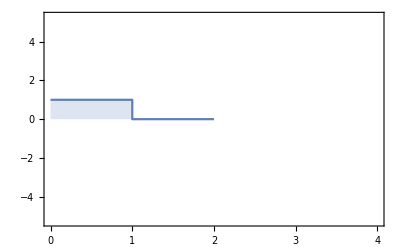
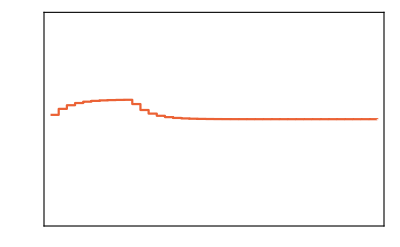
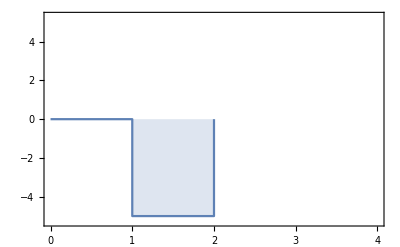
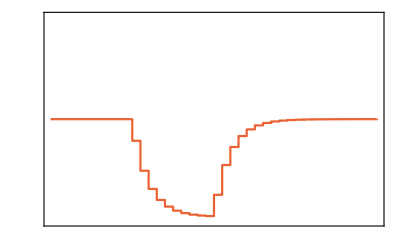

```mathematica
d=LinearDEDistortion[{{-5}},{1},1,2,40,1,0.1];
PulsePlot[ToPulse[{{1,1,0},{1,0,-5}},DistortionOperator->d],ShowDistortedPulse->True]
```

#### Example 3

Consider a tuned and matched resonator circuit with inductor L, resistor R, matching capacitor Cm, tuning capacitor Ct, and source resistance Rs. Kirchoff’s laws can be used to describe this circuit with the differential equation dx/dt=A.x(t)+f(t)b where x=(I_L
V_Cm
V_Ct) and f(t) is the forcing term (in Volts). The matrix A and the vector b are defined below. The circuit is in a frame rotating at angular rate ω_r (usually the resonance frequency of the circuit) so that real and imaginary components of x(t) correspond to in-phase and quadrature components, respectively. Our quantum system is being controlled by the magnetic field produced by the inductor, therefore our control amplitudes for the operators σ_x and σ_y will be proportional to the real and imaginary parts of I_L(t), respectively. The parameters are set to give a resonance frequency ω_r of roughly 10GHz.

```mathematica
Module[{L=1.689*^-10,R=0.01,Ct=1.47856*^-12,Cm=2.1256*^-14,Rs=50,ωr=2π 9.99967*^9},
A=({{-R/L-I ωr, 0, 1/L}, {0, -1/(Rs*Cm)-I ωr, -1/(Rs*Cm)}, {-1/(Ct), -1/(Rs*Ct), -1/(Rs Ct)-I ωr}});
b={0,1/(Rs Cm),1/(Rs Ct)};
]
```

Define a distortion operator based on this circuit. Note that all units are SI, so the time steps are on the order of ns.

```mathematica
d=LinearDEDistortion[A,b,1,10,100,5 10^-9,1 10^-9];
```

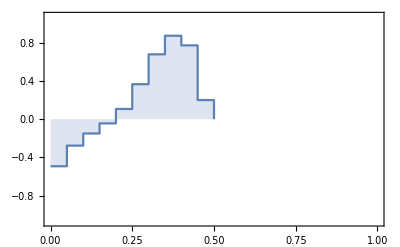
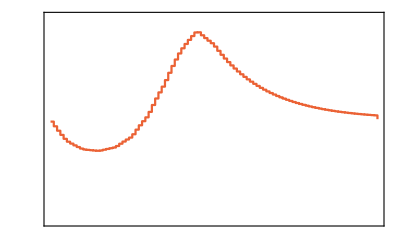
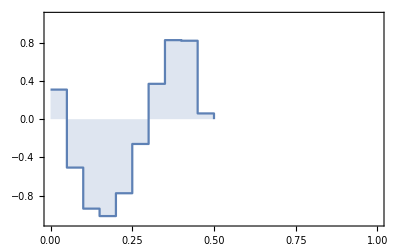
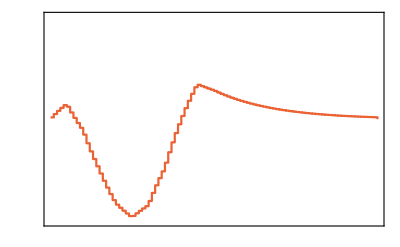

```mathematica
p=RandomSmoothPulse[5 10^-9,10,{{-1,1},{-1,1}}];
PulsePlot[ToPulse[p,DistortionOperator->d],ShowDistortedPulse->True]
```

### FrequencySpaceDistortion

FrequencySpaceDistortion[freqs,dt,M] returns a distortion function whose domain are frequency amplitudes of the specified frequencies. M is the number of points in the output pulse, each step with length dt.

The input pulse should have the same length as freqs, N, with format {{x1,a1,b1},{x2,a2,b2},...,{xN,aN,bN}}. The values of x don’t matter, and the output channel amplitudes are  calculated as channel_1=∑_(n=1)^N a_n(c⃗)_n+b_n(s⃗)_n and  channel_2=∑_(n=1)^N b_n(c⃗)_n-a_n(s⃗)_n where ((c⃗)_n)_m=cos(2π dt(m-1)f_n) and ((s⃗)_n)_m=sin(2π dt(m-1)f_n) for 1≤m≤M where f_n is the n^th element of freqs.

#### Example

```mathematica
d=FrequencySpaceDistortion[{1,2,3},0.05,100]
```

FrequencySpaceDistortion[{1,2,3}]

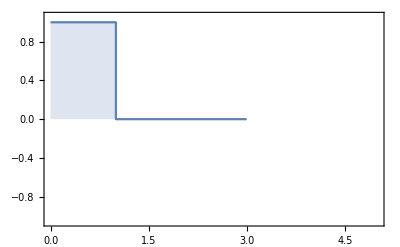
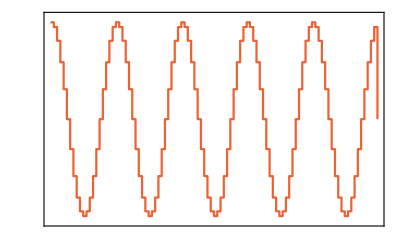
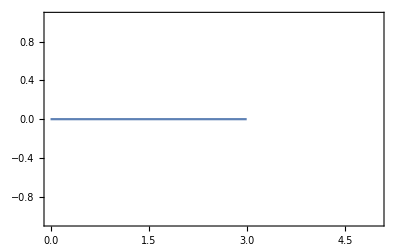
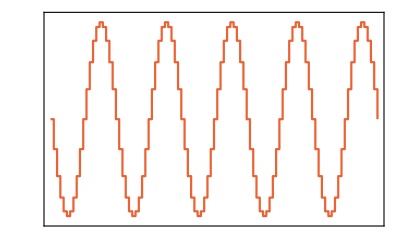

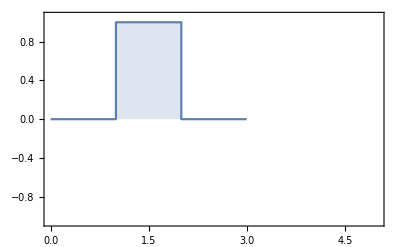
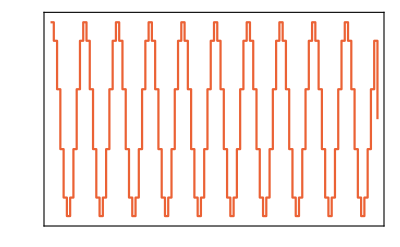
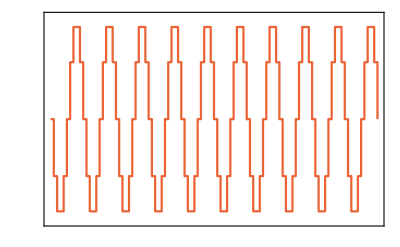
-Graphics--Graphics--Graphics--Graphics-

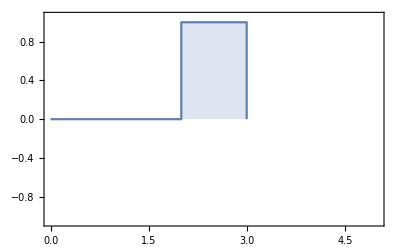
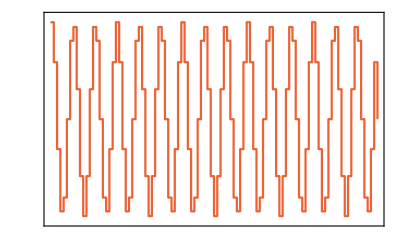
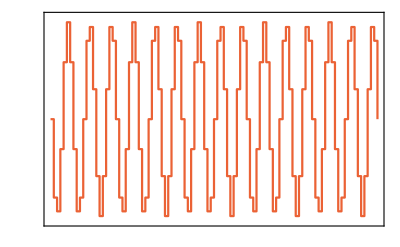
-Graphics--Graphics--Graphics--Graphics-

```mathematica
pulse=Pulse[TimeSteps->{1,1,1},Pulse->{{1,0},{0,0},{0,0}},DistortionOperator->d];
PulsePlot[pulse,ShowDistortedPulse->True]
pulse=Pulse[TimeSteps->{1,1,1},Pulse->{{0,0},{1,0},{0,0}},DistortionOperator->d];
PulsePlot[pulse,ShowDistortedPulse->True]
pulse=Pulse[TimeSteps->{1,1,1},Pulse->{{0,0},{0,0},{1,0}},DistortionOperator->d];
PulsePlot[pulse,ShowDistortedPulse->True]
```

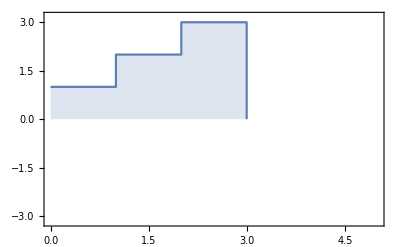
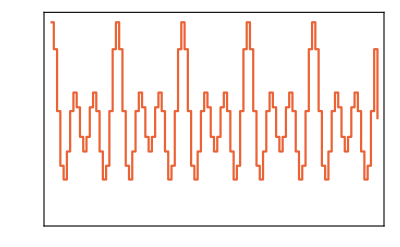
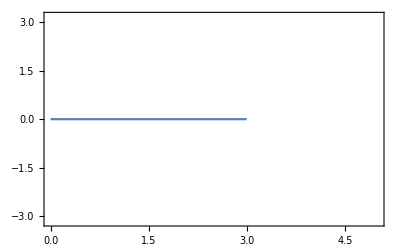
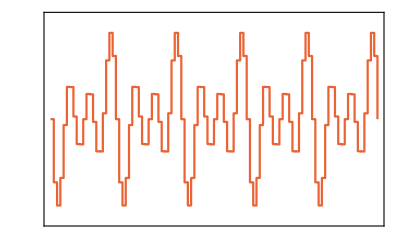

```mathematica
pulse=Pulse[TimeSteps->{1,1,1},Pulse->{{1,0},{2,0},{3,0}},DistortionOperator->d];
PulsePlot[pulse,ShowDistortedPulse->True]
```

### CompositePulseDistortion

CompositePulseDistortion[divisions,sequence] returns a distortion that emulates a composite pulse structure. divisions is a list of rules assigning symbols to indeces of the input pulse, and sequence is a list of the (possibly repeated) symbols representing the structure of the output pulse, where each one can be optionally phase rotated. It is assumed there are two input channels (for the phase rotations to work).

Example
For example, CompositePulseDistortion[{a->1;;30,b->31;;-1},{a,{b,π/3},{a,2π/3},b}] assigns the input pulse indeces 1;;30 and 31;;-1 to a and b, respectively. The output pulse will then be a concatenation of the segments a, followed by b phase rotated by π/3, followed by a phase rotated by 2π/3, and finally b.

#### Example

Assigns the input pulse indeces 1;;30 and 31;;-1 to a and b, respectively. The output pulse will then be a concatenation of the segments a, followed by b phase rotated by π/3, followed by a phase rotated by 2π/3, and finally b.

```mathematica
d= CompositePulseDistortion[{a->1;;30,b->31;;-1},{a,{b,π/3},{a,2π/3},b}];
```

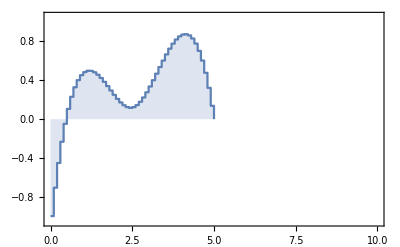
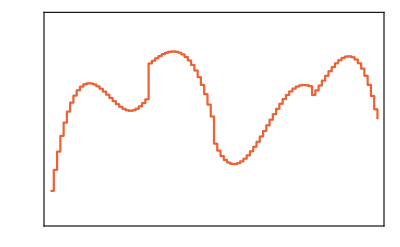
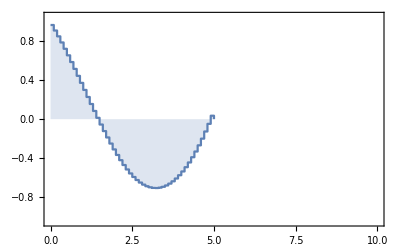
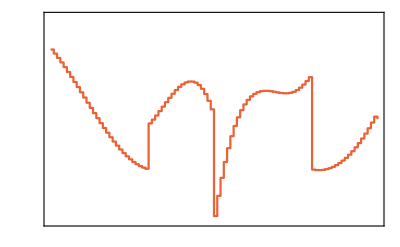

```mathematica
inputPulse=RandomSmoothPulse[ConstantArray[.1,50],{{-1,1},{-1,1}}];
pulse=Pulse[TimeSteps->inputPulse[[All,1]],Pulse->inputPulse[[All,2;;]],DistortionOperator->d];
PulsePlot[pulse,ShowDistortedPulse->True]
```

## Parameter Distributions

It is often necessary to optimize pulses over a distribution of system parameters. This is usually due to finite uncertainty of fixed paramaters, or paramaters that vary slowly in time within a known interval. These paramaters most often appear as error coeffecients in the system Hamiltonian and control Hamiltonians. For generality, this implementation of GRAPE additionally allows these parameters to appear in the penalty function, distortion operator, and target objective.

This distribution is input into FindPulse through the ParamaterDistribution option as a discrete probability distribution. See the documentation for ParameterDistribution for details on the expected format.

See ForceDistortionDependence if you plan on having distribution parameters within your distribution.

### ParameterDistributionMean

ParameterDistributionMean[distribution] returns the mean of the given distribution, where distribution is in the same format as accepted by the ParameterDistribution option to FindPulse. The return format is {symb1->mean1,symb2->mean2,...}.

#### Example

Take the mean over a normal distribution of α and β.

```mathematica
dist=RandomMultinormalParameterDistribution[{5,10},{2,2},{α,β},10000];
ParameterDistributionMean[dist]
```

{α→4.97901,β→10.0113}

### IdentityDistribution

IdentityDistribution[] returns a distribution with no parameters and a single point of probability 1. Explicitly, this is {{1}, {{}}}.

### ProductParameterDistribution

ProductParameterDistribution[dist1,dist2,dist3,...] returns a parameter distribution as accepted by the ParamterDistribution option to FindPulse which is the product distribution of the given parameter distributions.

#### Example

Take the product distribution of three parameter distributions.

```mathematica
ProductParameterDistribution[
{{1/5,2/5},{{α->1},{α->2}}},
UniformParameterDistribution[β->{0,0.1,3}],
RandomMultinormalParameterDistribution[{5,7},{1,1},{δ,γ},3]
]
```

{{0.0222222,0.0222222,0.0222222,0.0222222,0.0222222,0.0222222,0.0222222,0.0222222,0.0222222,0.0444444,0.0444444,0.0444444,0.0444444,0.0444444,0.0444444,0.0444444,0.0444444,0.0444444},{{α→1,β→-0.1,δ→4.59611,γ→5.99051},{α→1,β→-0.1,δ→5.39343,γ→8.12321},{α→1,β→-0.1,δ→5.77141,γ→6.89611},{α→1,β→0.,δ→4.59611,γ→5.99051},{α→1,β→0.,δ→5.39343,γ→8.12321},{α→1,β→0.,δ→5.77141,γ→6.89611},{α→1,β→0.1,δ→4.59611,γ→5.99051},{α→1,β→0.1,δ→5.39343,γ→8.12321},{α→1,β→0.1,δ→5.77141,γ→6.89611},{α→2,β→-0.1,δ→4.59611,γ→5.99051},{α→2,β→-0.1,δ→5.39343,γ→8.12321},{α→2,β→-0.1,δ→5.77141,γ→6.89611},{α→2,β→0.,δ→4.59611,γ→5.99051},{α→2,β→0.,δ→5.39343,γ→8.12321},{α→2,β→0.,δ→5.77141,γ→6.89611},{α→2,β→0.1,δ→4.59611,γ→5.99051},{α→2,β→0.1,δ→5.39343,γ→8.12321},{α→2,β→0.1,δ→5.77141,γ→6.89611}}}

### RandomSampleParameterDistribution

RandomSampleParameterDistribution[probDist,symbols,n] returns a parameter distribution as accepted by the ParameterDistribution option to FindPulse which is specified by pulling n random variates from the distribution probDist (e.g. NormalDistribution) with corresponding parameter symbols given by the list symbols.

RandomMultinormalParameterDistribution[μ,Σ,symbols,n]  returns a parameter distribution as accepted by the ParameterDistribution option to FindPulse which is specified by pulling n random variates from the distribution Normal(μ,Σ) where μ is the vector of means, and Σ is a list of standard deviations, or the covariance matrix. This is implemented using RandomSampleParameterDistribution.

RandomUniformParameterDistribution[minsAndMaxes,symbols,n]  returns a parameter distribution as accepted by the ParameterDistribution option to FindPulse which is specified by pulling n random variates from the distribution Unif(minsAndMaxes) where minsAndMaxes is list of tuples of minimums and maximums for each parameter. This is implemented using RandomSampleParameterDistribution.

#### Example 1

Make a distribution that is three points sampled from a Cauchy distribution.

```mathematica
RandomSampleParameterDistribution[CauchyDistribution[1,2],{α},3]
```

{{0.333333,0.333333,0.333333},{{α→1.98135},{α→0.590344},{α→-202.167}}}

#### Example 2

A multinormal distribution with finite covariance between α and β.

```mathematica
RandomMultinormalParameterDistribution[{5,10},{{1,.2},{.2,1}},{α,β},5]
```

{{0.2,0.2,0.2,0.2,0.2},{{α→4.04643,β→9.83357},{α→3.84049,β→8.91284},{α→2.83449,β→10.435},{α→5.50666,β→9.33858},{α→4.38625,β→8.68912}}}

#### Example 3

Random variates from the product distribution of Unif([0,1]) and Unif([10,11]).

```mathematica
RandomUniformParameterDistribution[{{0,1},{10,11}},{α,β},5]
```

{{0.2,0.2,0.2,0.2,0.2},{{α→0.263672,β→10.4727},{α→0.26617,β→10.896},{α→0.258419,β→10.3226},{α→0.294903,β→10.6796},{α→0.00409188,β→10.534}}}

### UniformParameterDistribution

UniformParamaterDistribution[symbol1→{mean1,width1,num1},...,symbolK→{meanK,widthK,numK}] returns a parameter distribution as accepted by the ParameterDistribution option to FindPulse which is the product distribution of K distributions, each with numk evenly spaced points ranging from meank-widthk to meank+widthk.

#### Example

```mathematica
UniformParameterDistribution[α->{0,1,3},β->{5,1,3}]
```

{{1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9},{{α→-1,β→4},{α→-1,β→5},{α→-1,β→6},{α→0,β→4},{α→0,β→5},{α→0,β→6},{α→1,β→4},{α→1,β→5},{α→1,β→6}}}

### TargetSelectDistribution

TargetSelectorDistribution[targetSymbol1→distribution1,targetSymbol2→distribution2,...] returns a modified ParameterDistribution which joins the given distributions while adding binary values to the corresponding targetSymbols.

For example, TargetSelectorDistribution[α→{{0.4,0.6},{γ→1}},β→{{0.2,0.8},{γ→2}}] returns {{0.3,0.2,0.3,0.2},{{α→1,β→0,γ→1},{α→1,β→0,γ→2},{β→1,α→0,γ→1},{β→1,α→0,γ→2}}}.

#### Example 1

Suppose we want a target desires one unitary for a certain set of parameters, but another unitary for another set of parameters. We can define the target

```mathematica
target=α TP[X]+β TP[Y];
```

And now the following distribution which dictates that when γ is 1, the target is an X gate, but when γ is 2, the target is a Y gate.

```mathematica
TargetSelectorDistribution[α->{{0.4,0.6},{γ->1}},β->{{0.2,0.8},{γ->2}}]
```

{{0.2,0.3,0.1,0.4},{{α→1,β→0,γ→1},{β→1,α→0,γ→2}}}

#### Example 2

Suppose we want a target which is a population inversion for some parameters, but a population maintainer for some other parameters. We can define the target

```mathematica
target=CoherentSubspaces[{({{1}, {0}}),({{0}, {1}})},{({{α}, {β}}),({{β}, {α}})}];
```

And now the following distribution which dictates that when γ is 1, the target is a population maintainer, but when γ is 2, the target is a population inverter.

```mathematica
TargetSelectorDistribution[α->{{0.4,0.6},{γ->1}},β->{{0.2,0.8},{γ->2}}]
```

{{0.2,0.3,0.1,0.4},{{α→1,β→0,γ→1},{β→1,α→0,γ→2}}}

## Pulse Penalties

PulsePenalty is an option to FindPulse which specifies a penalty to subtract from the utility function.

PulsePenalty[penalty] is a Head storing the function penalty which evaluates with the arguments penalty[inputPulse,computeGradient]. It holds that PulsePenalty[penalty][arguments]=penalty[arguments]; that is, PulsePenalty[penalty] is effectively callable with function values computed by penalty.

PulsePenalty[penalty,format] is equivalent to PulsePenalty[penalty], except that, additionally, a human readable format expression is included. Whenever Format[PulsePenalty[penalty,format]] is invoked, format is returned.

Function Arguments
•  The input pulse is expected in the same format as FindPulse’s argument initialGuess; {{dt1,a11,...,a1K},{dt2,a21,...,a2K},...,{dtN,aN1,...,aNK}} where the dt’s are pulse lengths and the a’s are input pulse amplitudes, and there are K input control channels and N input control time steps.
• If computeGradient is False, no gradient is returned, and the output is a number.
• If computeGradient is True, the output is of the form {p,gradient}, where p=penalty[pulse,False], and gradient is the gradient of the penalty function evaluated at the point pulse.

Notes
• The function FindPulse accepts the argument PulsePenalty, which should have a Head equalt to PulsePenalty and act as described above.
• In FindPulse, the pulse given to the pulse penalty function is the post-distorted pulse, and not the pre-distorted pulse.

### ZeroPenalty

ZeroPenalty[] is the default option for PulsePenalty to FindPulse. It returns a pulse that is constantly equal to 0.

### DemandValuePenalty

DemandValuePenalty[ϵ,m,r,qmax] returns a penalty function that goes to zero whenever (pulse-r)*m is zero. The argument m is the mask, a matrix the same shape as the pulse matrix without times, and r is a scalar or matrix the same shape as m with the desired values. qmax is the maximum possible difference between a pulse amplitude and (the corresponding element of) r, and ϵ is an overall scaling factor.

DemandValuePenalty is implemented with a soft maximum function; a function that behaves very much as max(|(pulse-r)*m|), but is differentiable.The exact function used is penalty=ϵ∑_(m,l=1,1)^(M,L) x_(m,l)ⅇ^(α x_(m,l))/(∑_(m,l=1,1)^(M,L) ⅇ^(α x_(m,l))) for α=1000 and x_(m,l)=|m*(pulse-r)|.

#### Example

Define a distortion and a DemandValuePenalty which wants the last 20 steps of the distorted pulse to be equal to 0.

```mathematica
distortion=LiftDistortionRank@ExponentialDistortion[0.1,10,70,0.1,0.02];
pulseMat=RandomSmoothPulse[0.1,10,{{-1,1},{-1,1}}];
penalty=DemandValuePenalty[1,Array[{1,1}If[#>=50,1,0]&,70],0,3]
```

DemandValuePenalty[0]

Here we see the penalty funciton value, the gradient of the penalty function at pulseMat, and a plot of pulseMat and its distorted version.

{0.195084,{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.333333,-1.14664×10^-59},{-3.81578×10^-8,-3.15508×10^-62},{-1.42625×10^-21,-4.17465×10^-66},{-9.53898×10^-33,-2.78064×10^-69},{-6.14073×10^-42,-6.9628×10^-72},{-1.76454×10^-49,-5.15877×10^-74},{-1.15973×10^-55,-9.29367×10^-76},{-9.96959×10^-61,-3.46622×10^-77},{-7.06276×10^-65,-2.34599×10^-78},{-2.81938×10^-68,-2.58657×10^-79},{-4.64119×10^-71,-4.25266×10^-80},{-2.4388×10^-73,-9.69821×10^-81},{-3.31593×10^-75,-2.89116×10^-81},{-9.82171×10^-77,-1.07329×10^-81},{-5.50422×10^-78,-4.7683×10^-82},{-5.19971×10^-79,-2.454×10^-82},{-7.53282×10^-80,-1.42455×10^-82},{-1.54878×10^-80,-9.12621×10^-83},{-4.24154×10^-81,-6.33809×10^-83},{-1.46893×10^-81,-4.70246×10^-83},{-6.16517×10^-82,-3.6829×10^-83}}}

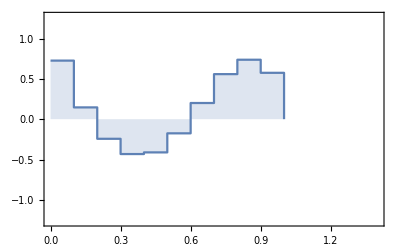
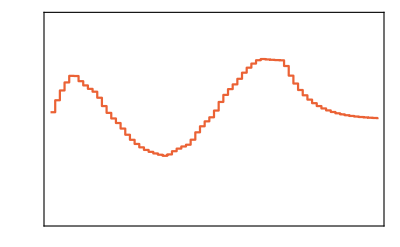
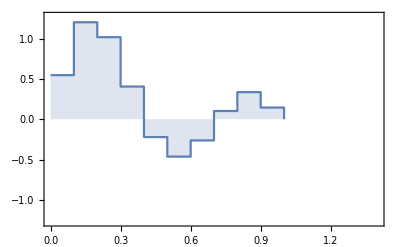
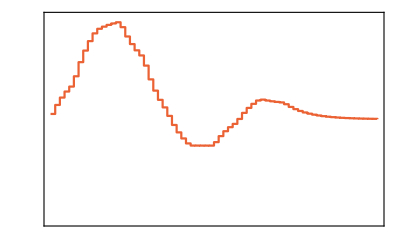

```mathematica
Print[penalty[distortion[pulseMat,False],True]]
PulsePlot[ToPulse[pulseMat,DistortionOperator->distortion],ShowDistortedPulse->True]
```

### RingdownPenalty

RingdownPenalty[ϵ,numRingdownSteps,qmax] returns a penalty function that attempts to make the last numRingdownSteps of the output pulse equal to 0. This is acheived by invoking DemandValuePenalty with value r=0 and an appropriate mask m.

#### Example

We create a RingdownPenalty and verify that it returns the same result as the DemandValuePenalty penalty example.

RingdownPenalty[20]

{0.167075,{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{-0.000936486,0.334596},{-0.000293872,-0.0000321223},{-4.88825×10^-16,-6.77154×10^-17},{-5.28252×10^-26,-1.02968×10^-26},{-3.22023×10^-34,-8.39786×10^-35},{-5.78203×10^-41,-1.9195×10^-41},{-1.69812×10^-46,-6.87695×10^-47},{-4.9656×10^-51,-2.36754×10^-51},{-9.57765×10^-55,-5.22089×10^-55},{-8.67773×10^-58,-5.27922×10^-58},{-2.794×10^-60,-1.85978×10^-60},{-2.54243×10^-62,-1.82176×10^-62},{-5.41862×10^-64,-4.1243×10^-64},{-2.31886×10^-65,-1.85443×10^-65},{-1.75633×10^-66,-1.46261×10^-66},{-2.1232×10^-67,-1.82773×10^-67},{-3.76399×10^-68,-3.32939×10^-68},{-9.12985×10^-69,-8.25725×10^-69},{-2.86264×10^-69,-2.6366×10^-69},{-1.10753×10^-69,-1.0354×10^-69},{-5.08972×10^-70,-4.81668×10^-70}}}

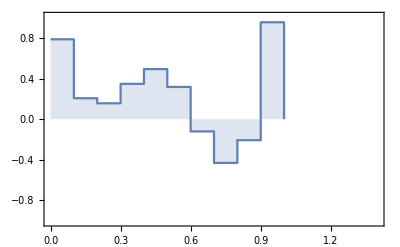
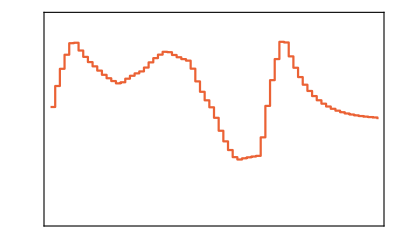
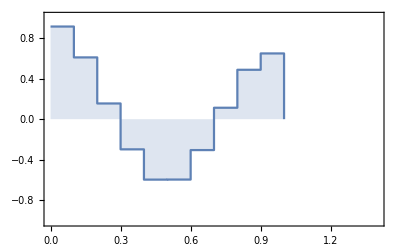
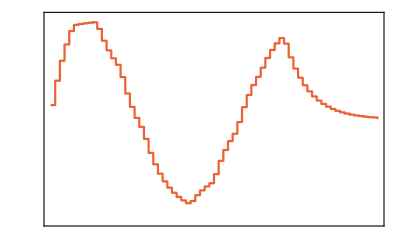

```mathematica
penalty=RingdownPenalty[1,20,3]
Print[penalty[distortion[pulseMat,False],True]]
PulsePlot[ToPulse[pulseMat,DistortionOperator->distortion],ShowDistortedPulse->True]
```

## Plotting Tools

### PulsePlot

PulsePlot[pulse] plots the pulse amplitudes of the Pulse object pulse. Each input channel is plotted on a separate subplot. The output pulse, as distorted by the DistortionOperator, is optionally plotted as well.

ListPlot Options
PulsePlot accepts all options which ListPlot accepts. When an option value is wrapped in DistributeOption, for example PlotLabel→DistributeOption[“channel1”,”channel2”,”channel3”], the successive arguments are individually sent to each subplot.
Several options to ListPlot are automatically set to produce quality pulse plots. These default values will be overridden if they are specified in PulsePlot. Changing certain of these options to do with frames and padding when ShowDistortedPulse is True may cause problems.

Options
In addition to the options of ListPlot, valid options for PulsePlot are:
• ShowDistortedPulse specifies whether the output pulse due to the DistortionOperator should be plotted. Valid values are False, True, All, and “Only”. If True, the output channels will be superimposed on the input channels. If “Only”, only the output pulse will be plotted. If All, the distorted pulse, the input pulse, and the modified input pulse will all be plotted (the modified input pulse will appear on the same scale as the input pulse).
• ChannelMapping specifies which output pulse channels should be plotted on top of which input pulse channels in the case that ShowDistortedPulse is True. The default value Automatic preserves channel order and attempts to spread the output channels as evenly as possible over the input channels; in the standard case where the number of input channels is equal to the number of output channels, this will be the expected 1 to 1 mapping. Enter this option as a list of lists of output channel indeces. For example, {{1,3},{2,4}} specifies that the first and third output channel are plotted on top of the first input channel, and the second and fourth output channel are plotted on top of the second output channel.
• PulseScaling specifies a set of axis scaling parameters. The default value None does not modify any scales. When ShowDistortedPulse is False, setting this option to {xscale,ampscale} multiplies the x-axis values by xscale, and the y-axis values by ampscale. ampscale can also be a list of length equal to the number of input channels, in which case each channel can have a different scaling. When ShowDistortedPulse is True, set this option to {xscale,inputAmpscale,outputAmpscale}.
• PulseLayout determines the layout of the pulse plot. Set to Row for a single row, Column for a single column,  {rows,columns} for a grid of a specified shape, or List for just a list of the plots with no layout.
• PulsePaddingMultiplier determines the vertical padding within a plot. This number is multiplied with the maximum absolute value of the plot amplitudes to determine the y limits. If set to a tuple, {inputMult,outputMult}, the input and output pulses get different multiplier paddings.

#### Options

ShowDistortedPulse is an option for PulsePlot and PulseFourierPlot which specifies whether the output pulse due to the DistortionOperator should be plotted. Valid values are False, True, and “Only”. If True, the output channels will be superimposed on the input channels, see ChannelMapping for configuration. If “Only”, only the output pulse will be plotted.

ChannelMapping is an option for PulsePlot and PulseFourierPlot which specifies which output pulse channels should be plotted on top of which input pulse channels. The default value Automatic preserves channel order and attempts to spread the output channels as evenly as possible over the input channels; in the standard case where the number of input channels is equal to the number of output channels, this will be the expected 1 to 1 mapping. Enter this option as a list of lists of output channel indeces. For example, {{1,3},{2,4}} specifies that the first and third output channel are plotted on top of the first input channel, and the second and fourth output channel are plotted on top of the second output channel.

PulseScaling is an option for PulsePlot which specifies a set of axis scaling parameters. The default value None does not modify any scales. When ShowDistortedPulse is False, setting this option to {xscale,ampscale} multiplies the x-axis values by xscale, and the y-axis values by ampscale. ampscale can also be a list of length equal to the number of input channels, in which case each channel can have a different scaling. When ShowDistortedPulse is True, set this option to {xscale,inputAmpscale,outputAmpscale}.

PulseLayout is an option for PulsePlot and FourierPulsePlot which determines the layout of the pulse plot. Set to Row for a single row, Column for a single column,  {rows,columns} for a grid of a specified shape, or List for just a list of the plots with no layout.

PulsePaddingMultiplier is an option for PulsePlot and PulseFourierPlot that determines the vertical padding within a plot. This number is multiplied with the maximum absolute value of the plot amplitudes to determine the y limits. If set to a tuple, {inputMult,outputMult}, the input and output pulses get different multiplier paddings.

#### Example 1

Barebones pulse plot.

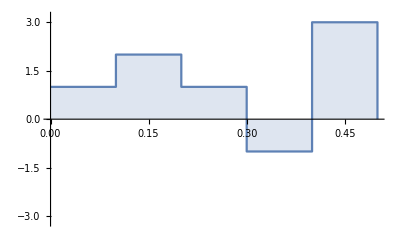
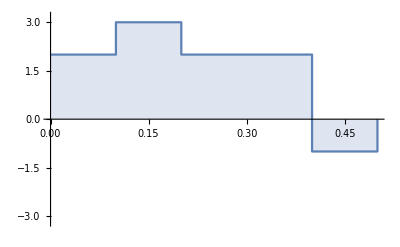

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2},{2,3},{1,2},{-1,2},{3,-1}}];
PulsePlot[pulse]
```

Same thing but with some styling and using DistributeOption.

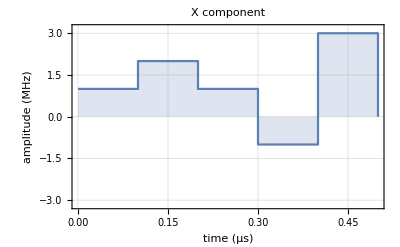
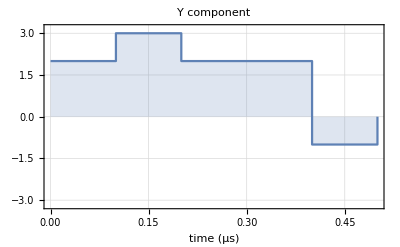

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2},{2,3},{1,2},{-1,2},{3,-1}}];
PulsePlot[pulse,PlotTheme->"Detailed",PlotLabel->DistributeOption[Style["X component",14,Bold],Style["Y component",14,Bold]],FrameLabel->DistributeOption[{"time (μs)","amplitude (MHz)"},{"time (μs)",""}]]
```

#### Example 2

First we define a distortion that involves a non-trivial All case; the modifiedInputPulse is the input pulse plus some constant steps appended.

```mathematica
d=LiftDistortionRank@DistortionOperator[
Function[{pulse,computeJac},If[computeJac===All,
{pulse,Join[pulse,{{0.05,-3},{0.05,-2}}],ExponentialDistortion[0.1,5,80,0.1,0.01][pulse,False]},
ExponentialDistortion[0.1,5,80,0.1,0.01][pulse,False]
]]];
```

Now look at the difference between ShowDistortedPulse being False, “Only”, True, and All.

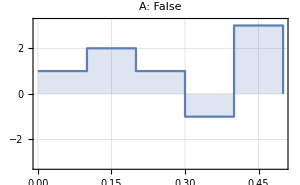
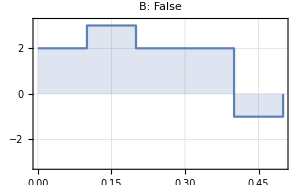
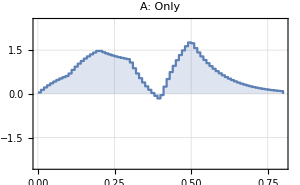
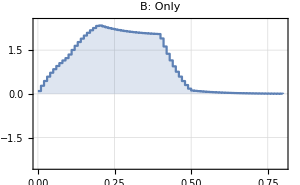
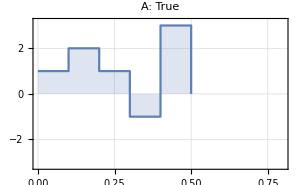
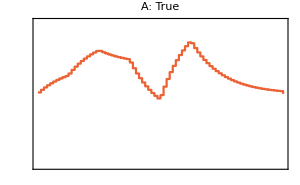
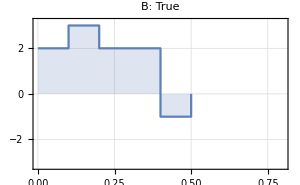
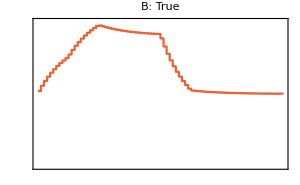

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2},{2,3},{1,2},{-1,2},{3,-1}},DistortionOperator->d];
Column[
PulsePlot[
pulse,
PlotLabel->DistributeOption["A: "<>ToString[#],"B: "<>ToString[#]],
ShowDistortedPulse->#,
ImageSize->300,
PlotTheme->"Detailed",
ImagePadding->{{25,25},{20,10}}
]&/@{False,"Only",True,All},
Frame->All
]
```

#### Example 3

Vary the PulsePaddingMultiplier.

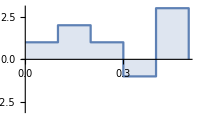
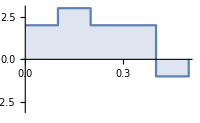
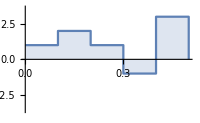
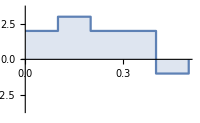
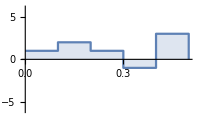
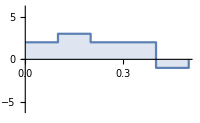

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2},{2,3},{1,2},{-1,2},{3,-1}}];
Column[PulsePlot[pulse,ImageSize->200,PulsePaddingMultiplier->#]&/@{1,1.2,2},Frame->All]
```

Vary the PulsePaddingMultiplier with ShowDistortedPulse->True.

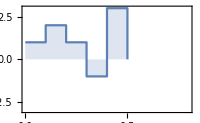
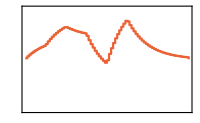
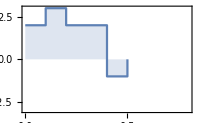
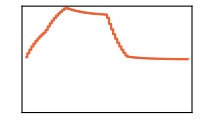
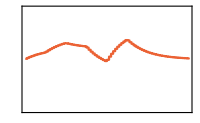
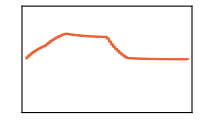
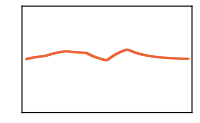
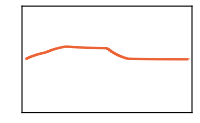
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2},{2,3},{1,2},{-1,2},{3,-1}},DistortionOperator->LiftDistortionRank@ExponentialDistortion[0.1,5,80,0.1,0.01]];
Column[PulsePlot[pulse,ShowDistortedPulse->True,ImageSize->200,PulsePaddingMultiplier->#]&/@{{1,1},{1,2},{1,4}},Frame->All]
```

#### Example 4

Various values of PulseLayout.

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2,3,4},{2,3,1,-2},{1,2,-1,2},{-1,2,-5,1},{3,-1,1,-2}}];
```

```mathematica
PulsePlot[pulse,ImageSize->200,PulseLayout->Row]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
PulsePlot[pulse,ImageSize->200,PulseLayout->{2,2}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
PulsePlot[pulse,ImageSize->200,PulseLayout->{2,3}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
PulsePlot[pulse,ImageSize->200,PulseLayout->Column]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
PulsePlot[pulse,ImageSize->200,PulseLayout->List]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Example 5

In this example we demonstrate possibilities for ChannelMapping when there are more output channels than input channels. The default behaviour is to spread out the output channels over the input channels as evenly as possible.

```mathematica
pulse=Pulse[TimeSteps->{0.1,0.1,0.1,0.1,0.1},Pulse->{{1,2},{2,3},{1,2},{-1,2},{3,-1}},DistortionOperator->VariableChangeDistortion[{Sqrt[Abs[a]],b+1,Sin[a],b/2},{a,b}]];
```

```mathematica
PulsePlot[pulse,ShowDistortedPulse->True,PlotLegends->DistributeOption[{"1","2"},{"3","4"}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
PulsePlot[pulse,ShowDistortedPulse->True,ChannelMapping->{{1,3},{2,4}},PlotLegends->DistributeOption[{"1","3"},{"2","4"}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
PulsePlot[pulse,ShowDistortedPulse->True,ChannelMapping->{{1,2,3},{4}},PlotLegends->DistributeOption[{"1","2","3"},{"4"}]]
```

-Graphics--Graphics--Graphics--Graphics-

### PulseFourierPlot

PulseFourierPlot is not yet implemented.

### RobustnessPlot

RobustnessPlot[pulse,symbol→{min,max,step},constantParams]plots the average fidelity of the given Pulse object pulse as a 1D function of the given parameter symbol in steps of step from min to max. The argument constantParams should be a list of replacement rules for any distribution symbols appearing in pulse that are not being plotted. 

RobustnessPlot[pulse,symbolX->{minX,maxX,stepX},symbolY->{minY,maxY,stepY},constantParams] plots the average fidelity of the given Pulse object pulse as a 2D function of the given parameters symbolX and symbolY in the given number of steps and range.

Notes
• Increasing the InterpolationOrder for 2D robustness plots can improve the figure’s appearance.
• Although related, the ParameterDistribution present in pulse is ignored by RobustnessPlot.
• The argument pulse requires the following keys for RobustnessPlot to function: TimeSteps, Pulse, InternalHamiltonian, ControlHamiltonians, Target, and DistortionOperator

Inherited Options
• For 1D robustness plots, options to ListPlot are valid when the option LogPlot is False, and options to ListLogPlot are valid when LogPlot is True.
• For 2D robustness plots, options to ListContourPlot are valid. Note that several options are set by default in order to produce quality robustness plots. These options, which can be overridden, are ColorFunction, ColorFunctionScaling, PlotLegends, ContourStyle, Contours, DataRange, and FrameLabel.
• For 2D robustness plots, when an option value is wrapped in DistributeOption, for example PlotLabel→DistributeOption[“channel1”,”channel2”,”channel3”], the successive arguments are individually sent to each subplot.

Options
• DistortionOperatorSweep when True indicates that the distortion contains a robustness parameter which is being swept and therefore needs to be calculated each time on the inner loop. Default is False.
• LogPlot can be True or False. For 1D robustness plots, this switches between ListPlot and ListLogPlot. For 2D robustness plots, this causes the default value of the Function option to be Log10(1-F) where F is average fidelity.
• Function can be Automatic, or a function of the average fidelity to be plotted.
• Grid is only for 2D robustness plots and can be Automatic or {rows,columns} and determines the layout shape of the subplots.
• LegendIsCell is only for 2D robustness plots and can be True or False. If True, the Legend is treated as the last element of the Grid, otherwise, the Legend is inserted on the last subplot.
• Alignment is only for 2D robustness plots and is passed to Grid.

#### Options

LegendIsCell is an option for 2D RobustnessPlot which when True, makes the legend its own figure which is put into the grid just like another plot.

DistortionOperatorSweep is an option for RobustnessPlot which when True indicates that the distortion contains a robustness parameter which is being swept and therefore needs to be calculated each time on the inner loop. Default is False.

#### Example 1

Create two π/2 pulses about the x axis with the minimum key requirements needed by RobustnessPlot.

```mathematica
pulse1=Pulse[
TimeSteps->{1/4},
Pulse->{{1,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
ControlHamiltonians->2π(1+γ){Spin[X][1/2],Spin[Y][1/2]},
Target->MatrixExp[-I (1/4)2π Spin[X][1/2]],
DistortionOperator->IdentityDistortion[]
];
pulse2=PulseReplaceKey[pulse1,TimeSteps,1/4+0.01];
```

Show the robustness to pulse amplitude imperfection (γ in the control Hamiltonians above).

```mathematica
RobustnessPlot[{pulse1,pulse2},γ->{-.2,.2,0.001},{δω->0},Joined->True,PlotRange->All,FrameLabel->{"γ","Log_10(1-F)"},PlotLegends->LineLegend[{"pulse1","pulse2"}],PlotTheme->"Detailed",PlotLabel->"Pulse Infidelity"]
```

-Graphics-

Same thing, but now LogPlot is False.

```mathematica
RobustnessPlot[{pulse1,pulse2},γ->{-.2,.2,0.001},{δω->0},Joined->True,PlotRange->All,FrameLabel->{"γ","F"},PlotLegends->LineLegend[{"pulse1","pulse2"}],PlotTheme->"Detailed",PlotLabel->"Pulse Fidelity",LogPlot->False]
```

-Graphics-

#### Example 2

We create the CORPSE and BB1 composite pulses for a π/2 gate about the x axis. For comparison, we also include a hard pulse.

(See Alway and Jones, 2007. Arbitrary precision composite pulses for NMR quantum computing. Journal of Magnetic Resonance 189, 114–120. for a summary of these two composite pulses).

```mathematica
corpse=Pulse[
TimeSteps->{1+.125-ArcSin[Sin[.125]/2],1-2ArcSin[Sin[.125]/2],.125-ArcSin[Sin[.125]/2]},
Pulse->{{1,0},{-1,0},{1,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
ControlHamiltonians->2π(1+γ){Spin[X][1/2],Spin[Y][1/2]},
Target->MatrixExp[-I (1/4)2π Spin[X][1/2]],
DistortionOperator->IdentityDistortion[]
];
bb1=Pulse[
TimeSteps->{0.5,1,0.5,0.25},
Pulse->{{-1/16,Sqrt[255]/16},{191/1024,Sin[3 ArcSec[-16]]},{-1/16,Sqrt[255]/16},{1,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
ControlHamiltonians->2π(1+γ){Spin[X][1/2],Spin[Y][1/2]},
Target->MatrixExp[-I (1/4)2π Spin[X][1/2]],
DistortionOperator->IdentityDistortion[]
];
hardpulse=Pulse[
TimeSteps->{1/4},
Pulse->{{1,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
ControlHamiltonians->2π(1+γ){Spin[X][1/2],Spin[Y][1/2]},
Target->MatrixExp[-I (1/4)2π Spin[X][1/2]],
DistortionOperator->IdentityDistortion[]
];
Column[PulsePlot[#,ImageSize->200]&/@{corpse,bb1,hardpulse},Frame->All]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

Compare the robustness profiles. Note that setting InterpolationOrder to more than 1 improves the appearance.

```mathematica
RobustnessPlot[{corpse,bb1,hardpulse},γ->{-.2,.2,0.01},δω->{-.5,.5,.05},{},PlotRange->{-5,1},ImageSize->300,PlotLabel->DistributeOption[Style["CORPSE",14,Bold],Style["BB1",14,Bold],Style["Hard Pulse",14,Bold]],FrameLabel->{Style["γ",14],Style["δω",14]},InterpolationOrder->2]
```

-Graphics- | -Graphics- | -Graphics- |

#### Example 3

Copy some pulse from a previous example.

```mathematica
corpse=Pulse[
TimeSteps->{1+.125-ArcSin[Sin[.125]/2],1-2ArcSin[Sin[.125]/2],.125-ArcSin[Sin[.125]/2]},
Pulse->{{1,0},{-1,0},{1,0}},
InternalHamiltonian->2π δω Spin[Z][1/2],
ControlHamiltonians->2π(1+γ){Spin[X][1/2],Spin[Y][1/2]},
Target->MatrixExp[-I (1/4)2π Spin[X][1/2]],
DistortionOperator->IdentityDistortion[]
];
```

Sometimes having LegendIsCell->True is better.

```mathematica
RobustnessPlot[ConstantArray[corpse,3],γ->{-.2,.2,0.01},δω->{-.5,.5,.05},{},PlotRange->{-5,1},ImageSize->230,InterpolationOrder->2,LegendIsCell->True,Grid->{2,2}]
```

-Graphics- | -Graphics-
-Graphics- |

But sometimes having LegendIsCell->False is better. In this case setting the Alignment to Left is helpful.

```mathematica
RobustnessPlot[ConstantArray[corpse,4],γ->{-.2,.2,0.01},δω->{-.5,.5,.05},{},PlotRange->{-5,1},ImageSize->230,InterpolationOrder->2,LegendIsCell->False,Grid->{2,2},Alignment->Left]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Distributed Options

DistributeOption allows you to distribute a given plotting option to each subplot of PulsePlot, PulseFourierPlot, or RobustnessPlot. For example, PlotLabel→DistributeOption[“X”,”Y”] will give the first subplot title “X” and the second sub plot title “Y”.

## Monitor Functions

### FidelityMonitor

FidelityMonitor[GRAPE,currentPulse,bestPulse,utilityList,abortButton] displays the utility value of the current pulse on a progress bar.

#### Example

Just plug in some made-up values to get a sense of what it looks like.

```mathematica
FidelityMonitor[Pause[5],ToPulse[{{0,0,0}},PenaltyValue->0,UtilityValue->.75],None,{},False]
```

### HistogramMonitor

HistogramMonitor[GRAPE,currentPulse,bestPulse,utilityList,abortButton] displays a histogram of utilitiy values in utilityList, the list of utilities found over Repetitions.

#### Example

Just plug in some made-up values to get a sense of what it looks like.

```mathematica
HistogramMonitor[Pause[5],ToPulse[RandomSmoothPulse[.1,30,{{-1,1},{-1,1}}],PenaltyValue->0,UtilityValue->.75],None,RandomReal[{.75,.8},100],False]
```

### PulsePlotMonitor

PulsePlotMonitor[] returns a function monitorFn[GRAPE,currentPulse,bestPulse,utilityList,abortButton] which displays a pulse plot of currentPulse and bestPulse. PulsePlotMonitor accepts all options that PulsePlot accepts, and passes them there.

#### Example

Just plug in some made-up values to get a sense of what it looks like.

```mathematica
distortion=LiftDistortionRank@ExponentialDistortion[0.1,10,70,0.1,0.02];
monitorFn=PulsePlotMonitor[ShowDistortedPulse->True];
monitorFn[Pause[5],ToPulse[RandomSmoothPulse[.1,10,{{-1,1},{-1,1}}],PenaltyValue->0,UtilityValue->.75,DistortionOperator->distortion],None,{},False]
```

## Gradient Ascent Tools

### Line Search Methods

QuadraticFitLineSearch[] returns a function lineSearch[initialUtility,testFn] which returns the best step size multiplier given the utility (including penalty) at the current pulse initialUtility and a function testFn[stepMultiplier] which evaluates the utiliity (including penalty) along the current step direction at a step multiplier of stepMultiplier. This is done by sampling testFn at 1 and 2, fitting the result (including initialUtility) to a parabola, and finding the maximum of the parabola. If the maximum appears to be beyond a value of 2, this procedure is repeated with samples of testFn at 2 and 4. The maximum parabola value is returned, clipped to a maximum value of 4.

Options
MinStepMul specifies the minimum multiplier to return. The default is 0.1

InterpolatedLineSearch[] returns a function lineSearch[initialUtility,testFn] which returns the best step size multiplier given the utility (including penalty) at the current pulse initialUtility and a function testFn[stepMultiplier] which evaluates the utiliity (including penalty) along the current step direction at a step multiplier of stepMultiplier. This is done by evaluating testFn at each of the values Range[min,max,step] and maximizing the interpolation of the result including initialUtility. This maximum value is returned, clipped between min and max. The quantities min, max and step are determined by options, shown below.

Options
MinStepMul provides min, default is 0.1.
MaxStepMul provides max, default is 4.1.
StepMulStep provides step, default is 1.

#### Options

MinStepMul provides the minimum line search step size multiplier for LineSearchMethods.

MaxStepMul is provides the maximum line search step size multiplier for LineSearchMethods.

StepMulStep provides the step size for line search step size multiplier finders in LineSearchMethods.

## Exporters

### ExportJCAMP

ExportJCAMP[filename,pulse] exports the Pulse object pulse in the JCAMP format as readable by Bruker NMR spectrometers. The pulse should have two control fields, x and y.

Options
JCAMPTitle, JCAMPDX, JCAMPDataType, JCAMPOrigin, JCAMPUser, JCAMPDate, JCAMPTime, JCAMPShapeExMode, JCAMPShapeToTrot, JCAMPShapeBWFac, JCAMPShapeIntegFac, JCAMPShapeMode, JCAMPCalibrationFactor

#### Options

Option | Default Value | Description
JCAMPTitle | Automatic | JCAMPTitle is an ExportJCAMP option with default value Automatic, which sets the title to the filename.Otherwise it should be a string.
JCAMPDX | "5.00 Bruker JCAMP library" | JCAMPDX is an ExportJCAMP option with default value '5.00 Bruker JCAMP library'.
JCAMPDataType | "Shape Data" | JCAMPDataType is an ExportJCAMP option with default value 'Shape Data'.
JCAMPOrigin | "Quantum-Utils Mathematica GRAPE" | JCAMPOrigin is an ExportJCAMP option with default value 'Quantum-Utils Mathematica GRAPE'.
JCAMPUser | "nmruser" | JCAMPUser is an ExportJCAMP option with default value 'nmruser'. Should be your username on the spectrometer.
JCAMPDate | Automatic | JCAMPDate is an ExportJCAMP option with default value Automatic, which sets the date to today.
JCAMPTime | Automatic | JCAMPTime is an ExportJCAMP option with default value Automatic, which uses the current time.
JCAMPShapeExMode | "None" | JCAMPShapeExMode is an ExportJCAMP option with default value 'None'.
JCAMPShapeToTrot | "9.000000e+01" | JCAMPShapeToTrot is an ExportJCAMP option with default value '9.000000e+01' (string, not number).
JCAMPShapeBWFac | "1.000000e+00" | JCAMPShapeBWFac is an ExportJCAMP option with default value '1.000000e+00' (string, not number).
JCAMPShapeIntegFac | "1.000000e+00" | JCAMPShapeIntegFac is an ExportJCAMP option with default value '1.000000e+00' (string, not number).
JCAMPShapeMode | "1" | JCAMPShapeMode is an ExportJCAMP option with default value '1' (string, not number).
JCAMPCalibrationFactor | 1 | JCAMPCalibrationFactor is an ExportJCAMP option with default being the integer 1. This is the number the amplitudes are divided by before writing to the JCAMP file.

### ExportSHP

ExportSHP[filename,pulse,scalePower,digits] exports a Pulse object pulse to a .shp file. This file has two columns, amplitude and phase, where amplitude is between 0 and 1 and phase is between 0 and 1 (1 refers to 1 circle, i.e. 2π in radians). The input pulse is assumed to have two control lines, x and y. The arguments scalePower and digits are optional. The default value for scalePower is Automatic, which divides the amplitudes by the maximum value in AmplitudeRange. If scalePower is a number, the amplitudes are normalized by this. The argument digits sets the number of digits written to file for each amplitude and phase. The default is 6.